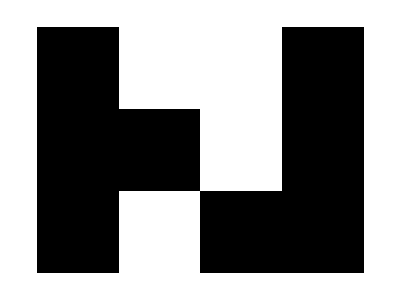

```mathematica
ArrayPlot[{
{1,0,0,1},
{1,1,0,1},
 {1,0,1,1}
}]
```

```mathematica
space = Table[0,{10},{10}]
```

{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

```mathematica
ArrayPlot[space]
```

-Graphics-

```mathematica
tile={{1,0,0},{1,1,1}}
```

{{1,0,0},{1,1,1}}

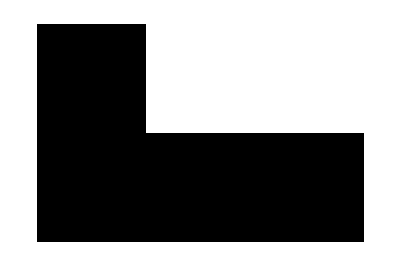

```mathematica
ArrayPlot[tile]
```

```mathematica
ArrayReshape[tile,{10,10}]
```

{{1,0,0,1,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

```mathematica
tile={{1,0,0},{1,1,1}}
```

{{1,0,0},{1,1,1}}

```mathematica
{r,c}=Dimensions[tile]
```

{2,3}

```mathematica
addrowsb=Table[0,{10-r},{10}]
```

{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

```mathematica
addcolsr=Table[0,r,{10-c}]
```

{{0,0,0,0,0,0,0},{0,0,0,0,0,0,0}}

```mathematica
Take[tile,2]
```

{{1,0,0},{1,1,1}}

```mathematica
tile[[{1,2}]]=MapThread[Join,{Take[tile,2],addcolsr}]
```

{{1,0,0,0,0,0,0,0,0,0},{1,1,1,0,0,0,0,0,0,0}}

```mathematica
tile=Join[tile,addrowsb]
```

{{1,0,0,0,0,0,0,0,0,0},{1,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

```mathematica
tile[[1]]
```

{1,0,0,0,0,0,0,0,0,0}

```mathematica
AppendTo[tile,{0,0,0}]
```

{{1,0,0,0,0,0,0,0,0,0},{1,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0}}

```mathematica
tile
```

{{1,0,0,0,0,0,0,0,0,0},{1,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0}}

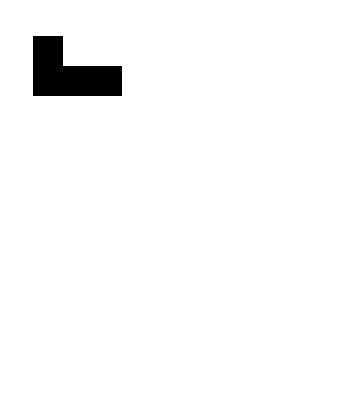

```mathematica
ArrayPlot[tile]
```

```mathematica
Transpose[tile]
```

Transpose::nmtx: The first two levels of {{1,0,0,0,0,0,0,0,0,0},{1,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0}} cannot be transposed.

Transpose[{{1,0,0,0,0,0,0,0,0,0},{1,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0}}]

```mathematica
Reverse/@tile
```

{{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,1,1,1},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0}}

```mathematica
tile={{1,0,0},{1,1,1}}
```

{{1,0,0},{1,1,1}}

```mathematica
allTiles[tile_]:=Module[{list={}},
AppendTo[list,tile];
AppendTo[list,Transpose[RotateLeft[tile]]];
AppendTo[list,Reverse/@RotateLeft[tile]];
AppendTo[list,Reverse/@RotateLeft[Transpose[RotateLeft[tile]]]];
AppendTo[list,RotateLeft[tile]];
AppendTo[list,Transpose[tile]];
AppendTo[list,Reverse/@tile];
AppendTo[list,RotateLeft[Transpose[RotateLeft[tile]]]];
list
]
```

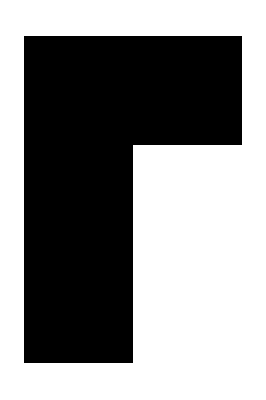
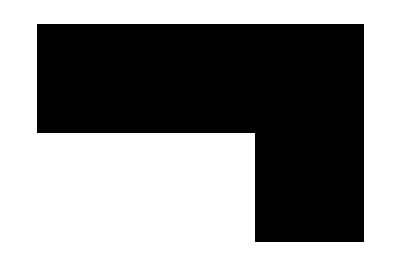
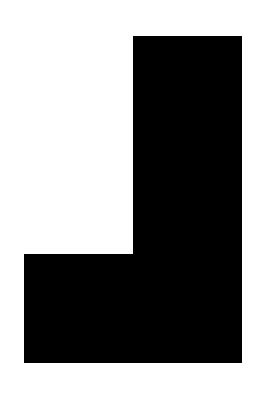
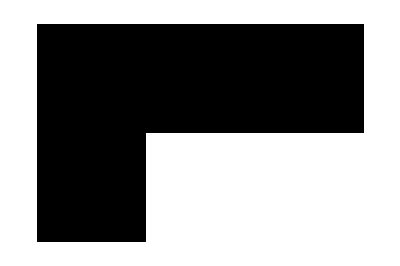
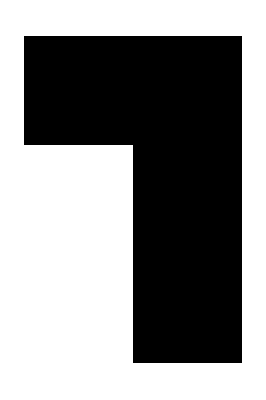
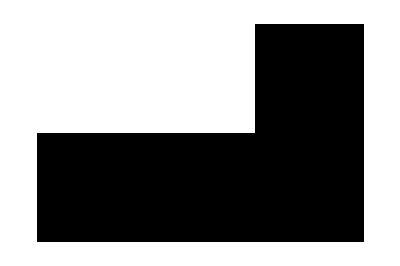
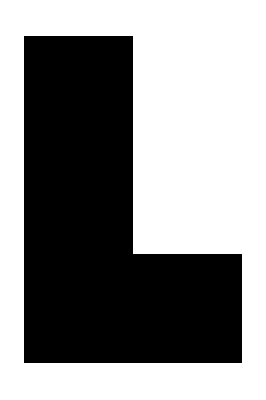
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[ArrayPlot[#,Frame->False]&,allTiles[tile]]
```

```mathematica
space
```

{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

```mathematica
Dimensions[space]
```

{10,10}

```mathematica
position={3,6}
```

{3,6}

```mathematica
tile
```

{{1,0,0},{1,1,1}}

```mathematica
Dimensions[tile]
```

{2,3}

```mathematica
Table[0,{Dimensions[tile][[1]]},{Dimensions[space][[2]]-Dimensions[tile][[2]]}]
```

{{0,0,0,0,0,0,0},{0,0,0,0,0,0,0}}

```mathematica
temptile=MapThread[Join,{
Table[0,{Dimensions[tile][[1]]},{position[[2]]-1}],
tile,
Table[0,{Dimensions[tile][[1]]},{10-(position[[2]]-1+Dimensions[tile][[2]])}]
}
]
```

{{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,1,1,0,0}}

```mathematica
addrowsa=Table[0,{position[[1]]-1},{10}]
```

{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

```mathematica
addrowsb=Table[0,{10-(position[[1]]-1+Dimensions[tile][[1]])},{10}]
```

{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

```mathematica
Join[addrowsa,temptile,addrowsb]
```

{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

```mathematica
positionTile[tile_,{x_,y_},{w_,h_}]:=Module[{temptile,addrowsa,addrowsb},
temptile=MapThread[Join,{Table[0,{Dimensions[tile][[1]]},{x-1}],tile,Table[0,{Dimensions[tile][[1]]},{w-(x-1+Dimensions[tile][[2]])}]
}
];
addrowsa=Table[0,{y-1},{w}];
addrowsb=Table[0,{h-(y-1+Dimensions[tile][[1]])},{w}];
Join[addrowsa,temptile,addrowsb]
]
```

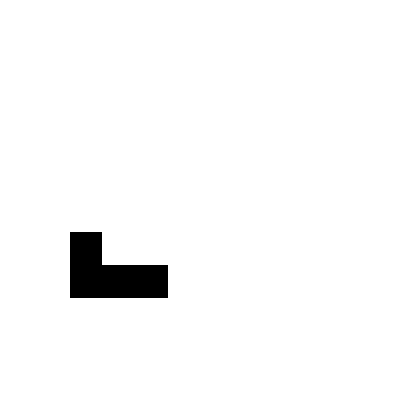

```mathematica
positionTile[tile,{2,7},{10,10}]//ArrayPlot
```

```mathematica
add=positionTile[tile,{2,7},{10,10}]+positionTile[tile,{2,4},{10,10}]
```

{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0},{0,1,1,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0},{0,1,1,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

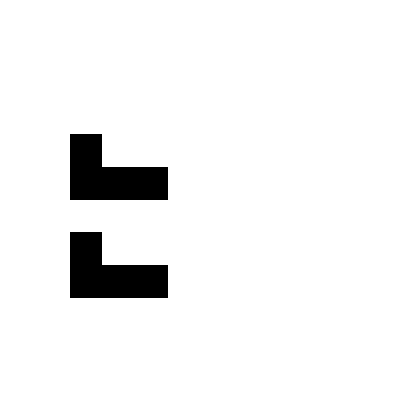

```mathematica
ArrayPlot[add]
```

```mathematica
Differences[MinMax[First/@Position[add,1]]]+1
```

{5}

```mathematica
Differences[MinMax[Last/@Position[add,1]]]+1
```

{3}

```mathematica
(Differences[MinMax[Last/@Position[add,1]]]+1)*(Differences[MinMax[First/@Position[add,1]]]+1)
```

{15}

```mathematica
add=positionTile[tiles[[1]],{2,7},{10,10}]+positionTile[tiles[[3]],{2,8},{10,10}]
```

{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0},{0,2,2,2,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

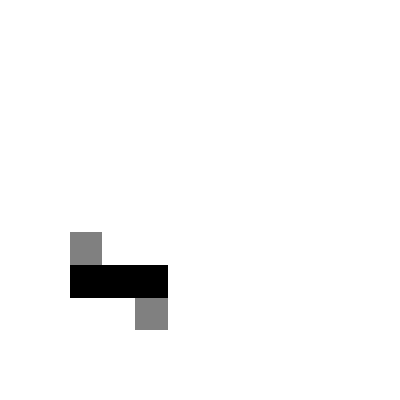

```mathematica
ArrayPlot[%]
```

```mathematica
(Differences[MinMax[Last/@Position[add,1]]]+1)*(Differences[MinMax[First/@Position[add,1]]]+1)
```

{1}

```mathematica
tiles = allTiles[tile]
```

{{{1,0,0},{1,1,1}},{{1,1},{1,0},{1,0}},{{1,1,1},{0,0,1}},{{0,1},{0,1},{1,1}},{{1,1,1},{1,0,0}},{{1,1},{0,1},{0,1}},{{0,0,1},{1,1,1}},{{1,0},{1,0},{1,1}}}

```mathematica
space
```

{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

```mathematica
ArrayPlot[%]
```

-Graphics-

```mathematica
increaseSpace[space_,d_,l_]:=Module[{newSpace},
If[d==1,
addrows=Table[0,{l},{Dimensions[space][[2]]}];
newSpace=Join[addrows,space];
];
If[d==3,
addrows=Table[0,{l},{Dimensions[space][[2]]}];
newSpace=Join[space,addrows];
];
If[d==2,
newSpace=MapThread[Join,{space,Table[0,{Dimensions[space][[1]]},{l}]}];
];
If[d==4,
newSpace=MapThread[Join,{Table[0,{Dimensions[space][[1]]},{l}],space}];
];
newSpace
]
```

```mathematica
addrowsa=Table[0,{4},{Dimensions[space][[2]]}]
```

{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

```mathematica
Join[space,addrowsa]//Dimensions
```

{14,10}

```mathematica
add=increaseSpace[add,2,2]
```

{{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0},{0,2,2,2,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
Table[0,{Dimensions[space][[1]]},{5}]
```

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

```mathematica
space//Dimensions
```

{10,10}

```mathematica
MapThread[Join,{space,Table[0,{Dimensions[space][[1]]},{5}]}]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
overlapQ[tile_,space_,{x_,y_}]:=Module[{},
delta=positionTile[tile,{x,y},Dimensions[space]];
Max[delta+space]!=1
]
```

```mathematica
overlapQ[tile,space,{3,3}]
```

False

```mathematica
tile={{1,0,0},{1,1,1}}
```

{{1,0,0},{1,1,1}}

```mathematica
delta=positionTile[tile,{3,3},{10,10}]+positionTile[tile,{3,1},{10,10}]+positionTile[tile,{6,3},{10,10}]
```

{{0,0,1,0,0,0,0,0,0,0},{0,0,1,1,1,0,0,0,0,0},{0,0,1,0,0,1,0,0,0,0},{0,0,1,1,1,1,1,1,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

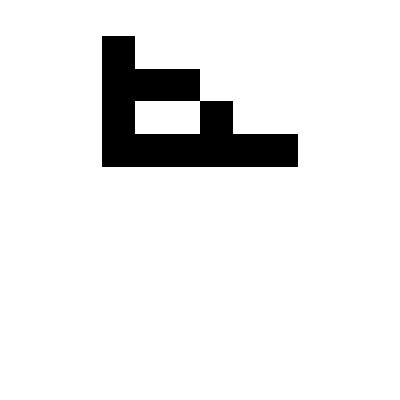

```mathematica
ArrayPlot[%201]
```

```mathematica
score[space_]:=Module[{},
If[detectVoid[space]==1,Infinity,
xRange=MinMax[Last/@Position[space,1]];
yRange=MinMax[First/@Position[space,1]];
First[(Differences[xRange]+1)*(Differences[yRange]+1)]
]
]
```

```mathematica
score[delta]
```

∞

```mathematica
delta//ArrayPlot
```

-Graphics-

```mathematica
xRange=MinMax[Last/@Position[delta,1]]
```

{3,8}

```mathematica
yRange=MinMax[First/@Position[delta,1]]
```

{1,4}

```mathematica
selectedRows=Take[delta,yRange]
```

{{0,0,1,0,0,0,0,0,0,0},{0,0,1,1,1,0,0,0,0,0},{0,0,1,0,0,1,0,0,0,0},{0,0,1,1,1,1,1,1,0,0}}

```mathematica
selectedRegion=Map[Take[#,xRange]&,selectedRows]
```

{{1,0,0,0,0,0},{1,1,1,0,0,0},{1,0,0,1,0,0},{1,1,1,1,1,1}}

```mathematica
detectVoid[space_]:=Module[{},
xRange=MinMax[Last/@Position[space,1]];
yRange=MinMax[First/@Position[space,1]];
selectedRows=Take[space,yRange];
selectedRegion=Map[Take[#,xRange]&,selectedRows];
img=Image[selectedRegion,"Bit"];
IntegerPart[Max[ImageData[FillingTransform[img,Padding->0,CornerNeighbors->True]-FillingTransform[img,Padding->0,CornerNeighbors->False]]]]
]
```

```mathematica
img=Image[delta,"Bit"]
```

-Graphics-

```mathematica
nimg=Binarize[ColorNegate@RemoveAlphaChannel[ColorConvert[img,"Grayscale"],White]]
```

-Graphics-

```mathematica
IntegerPart[Max[ImageData[FillingTransform[img,Padding->0,CornerNeighbors->True]-FillingTransform[img,Padding->0,CornerNeighbors->False]]]]
```

0

```mathematica
Subtract[FillingTransform[img,Padding->0,CornerNeighbors->True],img]
```

-Graphics-

```mathematica
detectVoid[space]
```

0

```mathematica
space
```

{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

```mathematica
tile
```

{{1,0,0},{1,1,1}}

```mathematica
addTile[tile_,space_,{x_,y_}]:=Module[{},
If[overlapQ[tile,space,{x,y}]==True,0,
space+positionTile[tile,{x,y},Dimensions[space]]
]
]
```

```mathematica
overlapQ[tile,space,{1,1}]
```

False

```mathematica
tempspace=space+positionTile[tile,{1,1},Dimensions[space]]
```

{{1,0,0,0,0,0,0,0,0,0},{1,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

```mathematica
!overlapQ[tile,tempspace,{1,1}]==False
```

True

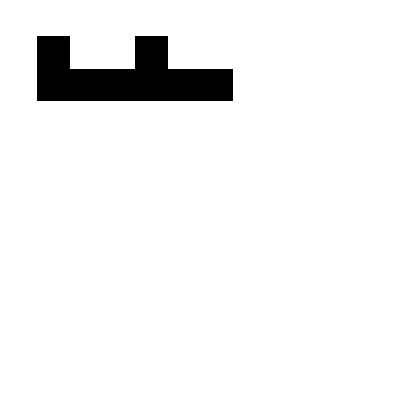

```mathematica
addTile[tile,tempspace,{4,1}]//ArrayPlot
```

```mathematica
space
```

{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

```mathematica
space=addTile[tile,space,{3,4}]
```

{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,0,1,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

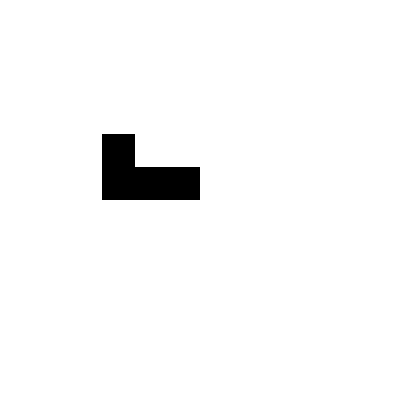

```mathematica
space//ArrayPlot
```

```mathematica
space=addTile[tile,space,{6,4}]
```

{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,1,0,0,0,0},{0,0,1,1,1,1,1,1,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

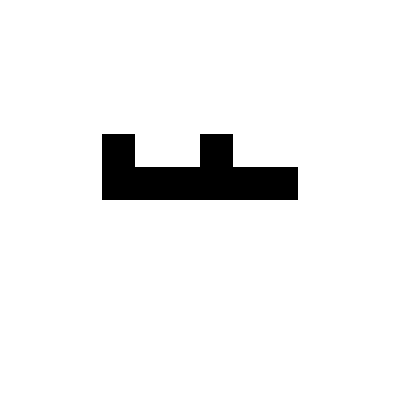

```mathematica
ArrayPlot[space]
```

```mathematica
Dimensions[tile]
```

{2,3}

```mathematica
usedRange[space]
```

{{3,8},{4,5}}

```mathematica
score[space]
```

12

```mathematica
Position[space,1]
```

{{4,3},{4,6},{5,3},{5,4},{5,5},{5,6},{5,7},{5,8}}

```mathematica
space=addTile[tiles[[4]],space,{4,2}]
```

{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,1,1,1,1,0,0,0,0},{0,0,1,1,1,1,1,1,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

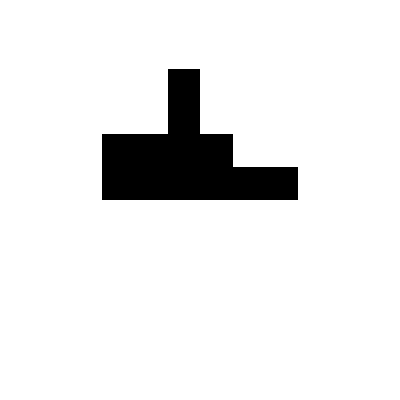

```mathematica
space//ArrayPlot
```

```mathematica
space
```

{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,1,1,1,1,0,0,0,0},{0,0,1,1,1,1,1,1,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

```mathematica
usedRange[space]
```

{{3,8},{2,5}}

```mathematica
Dimensions[tile]
```

{2,3}

```mathematica
tile//ArrayPlot
```

-Graphics-

```mathematica
scanRange[tile_,space_]:=Module[{},
xRange=usedRange[space][[1]];
yRange=usedRange[space][[2]];
{h,w}=Dimensions[tile];
{hMax,wMax}=Dimensions[space];
{{Max[xRange[[1]]-w,1],Min[xRange[[2]]+w,wMax-w+1]},{Max[yRange[[1]]-h,1],Min[yRange[[2]]+h,hMax-h+1]}}
]
```

```mathematica
tile=tiles[[3]]
```

{{1,1,1},{0,0,1}}

```mathematica
scanRange[tile,space]
```

{{1,7},{2,8}}

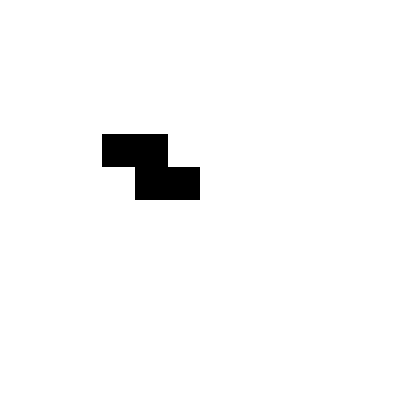

```mathematica
space//ArrayPlot
```

```mathematica
regiontoscan=scanRange[tile,space]
```

{{1,6},{2,6}}

```mathematica
scores=Transpose[Table[score[addTile[tile,space,{x,y}]],{x,regiontoscan[[1,1]],regiontoscan[[1,2]]},{y,regiontoscan[[2,1]],regiontoscan[[2,2]]}]]
```

{{20,16,12,16,20,24},{∞,∞,∞,∞,∞,18},{10,∞,∞,∞,∞,12},{15,∞,9,∞,∞,18},{20,16,12,16,20,24}}

```mathematica
TableForm[scores]
```

20 | 16 | 12 | 16 | 20 | 24
∞ | ∞ | ∞ | ∞ | ∞ | 18
10 | ∞ | ∞ | ∞ | ∞ | 12
15 | ∞ | 9 | ∞ | ∞ | 18
20 | 16 | 12 | 16 | 20 | 24

```mathematica
newPos=Reverse[Position[scores,Min[scores]][[1]]]+First/@regiontoscan-{1,1}
```

{3,5}

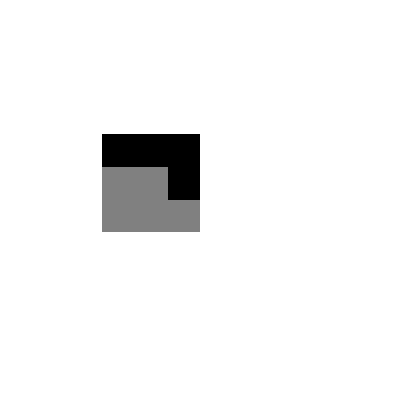

```mathematica
ArrayPlot[space+addTile[tile,space,newPos]]
```

```mathematica
regiontoscan=scanRange[tile,space];
scores=Transpose[Table[score[addTile[tile,space,{x,y}]],{x,regiontoscan[[1,1]],regiontoscan[[1,2]]},{y,regiontoscan[[2,1]],regiontoscan[[2,2]]}]];
scoresImg=Transpose[Table[scoreImg[addTile[tile,space,{x,y}]],{x,regiontoscan[[1,1]],regiontoscan[[1,2]]},{y,regiontoscan[[2,1]],regiontoscan[[2,2]]}]];
scores=scores/Max[Cases[{Infinity,1,2,4,10},_Integer]]*(1-scoresImg);
TableForm[scores]
newPos=Reverse[First[Take[Position[scores,Min[scores]],1]]]+First/@regiontoscan-{1,1};
space=addTile[tile,space,newPos]
ArrayPlot[space]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2.99608
∞ | ∞ | ∞ | ∞ | ∞ | 2.23373 | 2.30902 | 2.62588 | 2.99608
∞ | ∞ | ∞ | ∞ | ∞ | 2.83922 | 2.91765 | 3.31765 | 3.7451
∞ | ∞ | ∞ | ∞ | 3.42588 | 3.42588 | 3.52 | 4.00235 | 4.51765
4.08471 | 4.10667 | 4.08471 | 4.04078 | 4.10667 | 4.10667 | 4.17255 | 4.71882 | 5.29804

{{0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

-Graphics-

```mathematica
tile = {{1,1,1},{0,1,1}}
```

{{1,1,1},{0,1,1}}

```mathematica
ArrayPlot[tile]
```

-Graphics-

```mathematica
mirror[tile_]:=Module[{line,tmirror},For[i=1,i≤Length[tile],i++,line={};
For[j=Length[tile[[1]]],j≥1,j--,AppendTo[line,tile[[i,j]]];];
AppendTo[tmirror,line];]]
```

```mathematica
rotate={};
For[i=1,i≤Length[tile],i++,
line={};
For[j=Length[tile[[1]]], j≥1,j--,
AppendTo[line,tile[[i,j]]];
];
AppendTo[rotate,line]
]
```

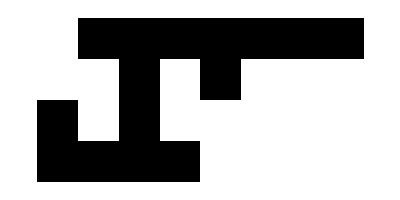
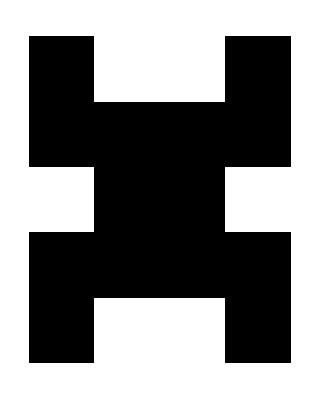
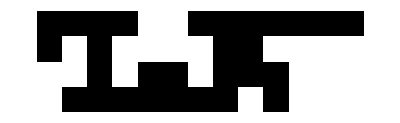

```mathematica
ArrayPlot/@tiles
```

```mathematica
tiles=Flatten[allTiles/@tiles,1]
```

{{{0,1,1,1,1,1,1,1},{0,0,1,0,1,0,0,0},{1,0,1,0,0,0,0,0},{1,1,1,1,0,0,0,0}},{{1,1,0,0},{1,0,0,1},{1,1,1,1},{1,0,0,1},{0,0,1,1},{0,0,0,1},{0,0,0,1},{0,0,0,1}},{{0,0,0,0,1,1,1,1},{0,0,0,0,0,1,0,1},{0,0,0,1,0,1,0,0},{1,1,1,1,1,1,1,0}},{{1,0,0,0},{1,0,0,0},{1,0,0,0},{1,1,0,0},{1,0,0,1},{1,1,1,1},{1,0,0,1},{0,0,1,1}},{{1,1,1,1,1,1,1,0},{0,0,0,1,0,1,0,0},{0,0,0,0,0,1,0,1},{0,0,0,0,1,1,1,1}},{{0,0,0,1},{0,0,0,1},{0,0,0,1},{0,0,1,1},{1,0,0,1},{1,1,1,1},{1,0,0,1},{1,1,0,0}},{{1,1,1,1,0,0,0,0},{1,0,1,0,0,0,0,0},{0,0,1,0,1,0,0,0},{0,1,1,1,1,1,1,1}},{{0,0,1,1},{1,0,0,1},{1,1,1,1},{1,0,0,1},{1,1,0,0},{1,0,0,0},{1,0,0,0},{1,0,0,0}},{{1,0,0,1},{1,1,1,1},{0,1,1,0},{1,1,1,1},{1,0,0,1}},{{1,1,0,1,1},{0,1,1,1,0},{0,1,1,1,0},{1,1,0,1,1}},{{1,1,1,1,0,0,1,1,1,1,1,1,1},{1,0,1,0,0,0,0,1,1,0,0,0,0},{0,0,1,0,1,1,0,1,1,1,0,0,0},{0,1,1,1,1,1,1,1,0,1,0,0,0}},{{0,0,1,1},{1,0,0,1},{1,1,1,1},{1,0,0,1},{1,1,0,0},{1,1,0,0},{1,0,0,1},{1,1,1,1},{0,1,1,1},{1,1,0,1},{0,0,0,1},{0,0,0,1},{0,0,0,1}},{{0,0,0,1,0,1,1,1,1,1,1,1,0},{0,0,0,1,1,1,0,1,1,0,1,0,0},{0,0,0,0,1,1,0,0,0,0,1,0,1},{1,1,1,1,1,1,1,0,0,1,1,1,1}},{{1,0,0,0},{1,0,0,0},{1,0,0,0},{1,0,1,1},{1,1,1,0},{1,1,1,1},{1,0,0,1},{0,0,1,1},{0,0,1,1},{1,0,0,1},{1,1,1,1},{1,0,0,1},{1,1,0,0}},{{1,1,1,1,1,1,1,0,0,1,1,1,1},{0,0,0,0,1,1,0,0,0,0,1,0,1},{0,0,0,1,1,1,0,1,1,0,1,0,0},{0,0,0,1,0,1,1,1,1,1,1,1,0}},{{0,0,0,1},{0,0,0,1},{0,0,0,1},{1,1,0,1},{0,1,1,1},{1,1,1,1},{1,0,0,1},{1,1,0,0},{1,1,0,0},{1,0,0,1},{1,1,1,1},{1,0,0,1},{0,0,1,1}},{{0,1,1,1,1,1,1,1,0,1,0,0,0},{0,0,1,0,1,1,0,1,1,1,0,0,0},{1,0,1,0,0,0,0,1,1,0,0,0,0},{1,1,1,1,0,0,1,1,1,1,1,1,1}},{{1,1,0,0},{1,0,0,1},{1,1,1,1},{1,0,0,1},{0,0,1,1},{0,0,1,1},{1,0,0,1},{1,1,1,1},{1,1,1,0},{1,0,1,1},{1,0,0,0},{1,0,0,0},{1,0,0,0}}}

```mathematica
rotate//ArrayPlot
```

-Graphics-

```mathematica
Transpose[rotate]//ArrayPlot
```

-Graphics-

```mathematica
tile={{1,0},{1,0},{1,1}}
```

{{1,0},{1,0},{1,1}}

```mathematica
mirrorv[tile_]:=Module[{line={},tMirror={}},
tMirror={};
For[i=1,i≤Length[tile],i++,
line={};
For[j=Length[tile[[1]]],j≥1,j--,
AppendTo[line,tile[[i,j]]];
];
AppendTo[tMirror,line];
];
tMirror
]
```

```mathematica
mirrorv[tile]//ArrayPlot
```

-Graphics-

```mathematica
tile//ArrayPlot
```

-Graphics-

```mathematica
rotatec[tile_]:=Module[{line={},tMirror={}},
tMirror={};
For[i=1,i≤Length[tile[[1]]],i++,
line={};
For[j=Length[tile],j≥1,j--,
AppendTo[line,tile[[j,i]]];
];
AppendTo[tMirror,line];
];
tMirror
]
```

```mathematica
rotatec[tile]//ArrayPlot
```

-Graphics-

```mathematica
ArrayPlot/@NestList[rotatec,mirrorv[tile],3]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
tile//ArrayPlot
```

-Graphics-

```mathematica
DeleteDuplicates[%]
```

{{{1,0},{1,1},{0,1}},{{0,1,1},{1,1,0}},{{0,1},{1,1},{1,0}},{{1,1,0},{0,1,1}}}

```mathematica
NestList[rotatec,tile,3]
```

{{{1,0},{1,0},{1,1}},{{1,1,1},{1,0,0}},{{1,1},{0,1},{0,1}},{{0,0,1},{1,1,1}}}

```mathematica
space
```

{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

```mathematica
space//ArrayPlot
```

-Graphics-

```mathematica
space//ArrayPlot
```

-Graphics-

```mathematica
space+positionTile[tile,{4,5},{10,10}]+positionTile[tile,{4,7},{10,10}]
```

{{0,0,0,0,0,0,0,0,0,0},{0,1,1,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,1,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,1,1,1,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

```mathematica
ArrayPlot[space+positionTile[tile,{4,5},{10,10}]+positionTile[tile,{4,7},{10,10}]]
```

-Graphics-

```mathematica
ArrayPlot[space+positionTile[tile,{4,5},{10,10}]+positionTile[tile,{5,4},{10,10}]]
```

-Graphics-

```mathematica
Max[1-ImageData[Blur[Downsample[Rasterize[ArrayPlot[space+positionTile[tile,{4,5},{10,10}]+positionTile[tile,{5,4},{10,10}]]],5,5],20]]]
```

0.435294

```mathematica
Max[1-ImageData[Blur[Downsample[Rasterize[ArrayPlot[space+positionTile[tile,{4,5},{10,10}]+positionTile[tile,{4,7},{10,10}]]],5,5],20]]]
```

0.392157

```mathematica
Max[1-ImageData[Blur[Downsample[Rasterize[ArrayPlot[space+positionTile[tile,{4,5},{10,10}]+positionTile[tile,{5,4},{10,10}]]],5,5],20]]]
```

0.435294

```mathematica
space//ArrayPlot
```

-Graphics-

```mathematica
{{1,2},{3,4}}/Max[{{1,2},{3,4}}]//N
```

{{0.25,0.5},{0.75,1.}}

```mathematica
Cases[{Infinity,1,2,4,10},_Integer]
```

{1,2,4,10}

```mathematica
minScores={};
For[i=1,i≤Length[tiles],i++,
tile=tiles[[i]];
regiontoscan=scanRange[tile,space];
scores=Transpose[Table[score[addTile[tile,space,{x,y}]],{x,regiontoscan[[1,1]],regiontoscan[[1,2]]},{y,regiontoscan[[2,1]],regiontoscan[[2,2]]}]];
scoresImg=Transpose[Table[scoreImg[addTile[tile,space,{x,y}]],{x,regiontoscan[[1,1]],regiontoscan[[1,2]]},{y,regiontoscan[[2,1]],regiontoscan[[2,2]]}]];
scores=scores/Max[Cases[{Infinity,1,2,4,10},_Integer]]*(1-scoresImg);
newPos=Reverse[First[Take[Position[scores,Min[scores]],1]]]+First/@regiontoscan-{1,1};
AppendTo[minScores,{Min[scores],addTile[tile,space,newPos]}];
];
```

Take::take: Cannot take positions 1 through 1 in {}.

Thread::tdlen: Objects of unequal length in {}+{1,1}+{-1,-1} cannot be combined.

Take::take: Cannot take positions 1 through 1 in {}.

Thread::tdlen: Objects of unequal length in {}+{1,1}+{-1,-1} cannot be combined.

Take::take: Cannot take positions 1 through 1 in {}.

General::stop: Further output of Take::take will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {}+{1,1}+{-1,-1} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

```mathematica
First[SortBy[minScores,#[[1]]&]][[2]]//ArrayPlot
```

-Graphics-

```mathematica
visualSpace=visualSpace+(RandomReal[])*First[SortBy[minScores,#[[1]]&]][[2]];
```

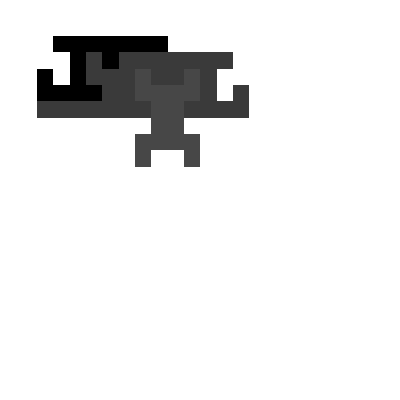

```mathematica
visualSpace//ArrayPlot
```

```mathematica
space//ArrayPlot
```

-Graphics-

```mathematica
spaceBak=space
```

{{0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
space=space[[10;;20]]
```

{{0,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
space=increaseSpace[space,3,9]
```

{{0,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
space=First[SortBy[minScores,#[[1]]&]][[2]];
```

```mathematica
SetSharedVariable[minScores];
minScores={};
ParallelMap[
tile=#;
regiontoscan=scanRange[tile,space];
scores=Transpose[Table[score[addTile[tile,space,{x,y}]],{x,regiontoscan[[1,1]],regiontoscan[[1,2]]},{y,regiontoscan[[2,1]],regiontoscan[[2,2]]}]];
scoresImg=Transpose[Table[scoreImg[addTile[tile,space,{x,y}]],{x,regiontoscan[[1,1]],regiontoscan[[1,2]]},{y,regiontoscan[[2,1]],regiontoscan[[2,2]]}]];
scores=scores/Max[Cases[{Infinity,1,2,4,10},_Integer]]*(1-scoresImg);
newPos=Reverse[First[Take[Position[scores,Min[scores]],1]]]+First/@regiontoscan-{1,1};
AppendTo[minScores,{Min[scores],addTile[tile,space,newPos]}];
&,tiles];
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

```mathematica
delta=Table[0,{10},{10}]
```

{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

```mathematica
delta=positionTile[tiles[[3]],{5,4},{10,10}]
```

{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,1,1,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

```mathematica
delta=addTile[tile,delta,{4,6}]
```

{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,1,1,0,0,0,0},{0,0,0,0,1,1,0,0,0,0},{0,0,0,1,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

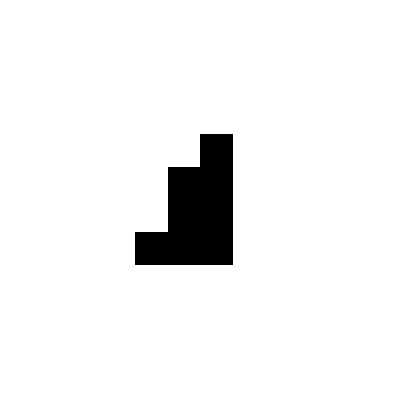

```mathematica
ArrayPlot[delta]
```

```mathematica
delta=addTile[tiles[[2]],delta,{4,4}]
```

{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,1,0,0,0,0},{0,0,0,1,1,1,0,0,0,0},{0,0,0,1,1,1,0,0,0,0},{0,0,0,1,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

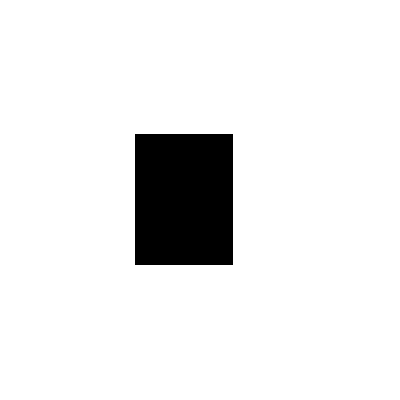

```mathematica
delta//ArrayPlot
```

```mathematica
delta=addTile[tiles[[3]],delta,{2,5}]
```

{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,1,0,0,0,0},{0,0,1,1,1,1,0,0,0,0},{0,1,1,1,1,1,0,0,0,0},{0,0,1,1,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

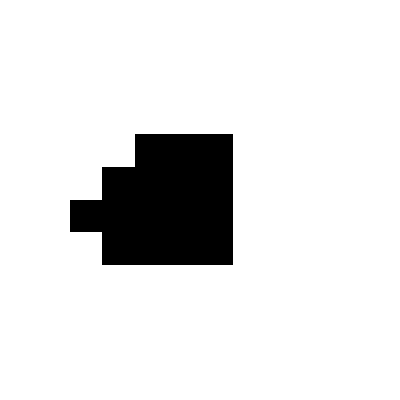

```mathematica
delta//ArrayPlot
```

```mathematica
xRange=MinMax[Last/@Position[space,1]];
yRange=MinMax[First/@Position[space,1]];
selectedRows=Take[space,yRange];
selectedRegion=Map[Take[#,xRange]&,selectedRows];
```

```mathematica
selectedRegion
```

{{1,1,1,0,0,1,0,0},{1,1,1,1,1,1,0,0},{0,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,0},{1,1,1,1,1,1,1,0},{1,1,0,1,1,1,0,0},{0,1,0,1,1,1,0,0}}

```mathematica
img=Image[selectedRegion,"Bit"]
```

-Graphics-

```mathematica
FillingTransform[img,Padding->0,CornerNeighbors->False]
```

-Graphics-

```mathematica
Dilation[img,4]
```

-Graphics-

```mathematica
regiontoscan=scanRange[tile,space];
scores=Transpose[Table[score[addTile[tile,space,{x,y}]],{x,regiontoscan[[1,1]],regiontoscan[[1,2]]},{y,regiontoscan[[2,1]],regiontoscan[[2,2]]}]];
```

```mathematica
scores//TableForm
```

∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 156
∞ | ∞ | ∞ | ∞ | ∞ | 126 | 140 | 154 | 168
∞ | ∞ | ∞ | ∞ | ∞ | 135 | 150 | 165 | 180
∞ | ∞ | ∞ | ∞ | 128 | 144 | 160 | 176 | 192
136 | 136 | 136 | 136 | 136 | 153 | 170 | 187 | 204

```mathematica
Position[scores,Min[scores]][[First[Position[Map[scoresImg[[#[[1]],#[[2]]]]&,Position[scores,Min[scores]]],Min[Map[scoresImg[[#[[1]],#[[2]]]]&,Position[scores,Min[scores]]]]]][[1]]]]
```

{2,6}

```mathematica
tile//ArrayPlot
```

-Graphics-

```mathematica
scoresImg=Transpose[Table[scoreImg[addTile[tile,space,{x,y}]],{x,regiontoscan[[1,1]],regiontoscan[[1,2]]},{y,regiontoscan[[2,1]],regiontoscan[[2,2]]}]];
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

```mathematica
scoresImg//TableForm
```

0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.305882
0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.396078 | 0.34902 | 0.341176 | 0.298039
0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.380392 | 0.356863 | 0.32549 | 0.329412 | 0.294118
0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.356863 | 0.34902 | 0.337255 | 0.345098 | 0.305882
0.356863 | 0.329412 | 0.337255 | 0.329412 | 0.321569 | 0.329412 | 0.317647 | 0.329412 | 0.294118

```mathematica
tempregion=positionTile[{{1,1,1},{0,0,1}},{5,7},{10,10}]+positionTile[{{1,1,1},{0,0,1}},{2,5},{10,10}]+positionTile[{{1,1,1},{0,0,1}},{5,5},{10,10}]
```

{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,0,0,0},{0,0,0,1,0,0,1,0,0,0},{0,0,0,0,1,1,1,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

```mathematica
img=Image[tempregion,"Bit"]
```

-Graphics-

```mathematica
FillingTransform[img,Padding->0,CornerNeighbors->True]
```

-Graphics-

```mathematica
Union[Flatten[ImageData[FillingTransform[img,Padding->0,CornerNeighbors->True]-img]]]
```

{0.,1.}

```mathematica
Max[Union[Flatten[ImageData@FillingTransform[img,CornerNeighbors->True]-ImageData@img]]]//RepeatedTiming
```

{0.0033,1}

```mathematica
SelectComponents[1-img,#EnclosingComponentCount==0&]
```

-Graphics-

```mathematica
RepeatedTiming[Values@ComponentMeasurements[tempregion,"Count"]==Values@ComponentMeasurements[tempregion,"FilledCount"]]
```

{0.00088,False}

```mathematica
Values@ComponentMeasurements[tempregion,"FilledCount"]
```

{14}

```mathematica
tempregion1=Table[1,{10},{10}]+positionTile[{{1,1,1},{0,0,1}},{2,2},{10,10}]
```

{{1,1,1,1,1,1,1,1,1,1},{1,2,2,2,1,1,1,1,1,1},{1,1,1,2,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1}}

```mathematica
Table[{Length[Union[Flatten[ImageData[Dilation[Image[selectedRegion,"Bit"],n]]]]],Dilation[Image[selectedRegion,"Bit"],n],n},{n,1,12}]
```

{{2,-Graphics-,1},{2,-Graphics-,2},{1,-Graphics-,3},{1,-Graphics-,4},{1,-Graphics-,5},{1,-Graphics-,6},{1,-Graphics-,7},{1,-Graphics-,8},{1,-Graphics-,9},{1,-Graphics-,10},{1,-Graphics-,11},{1,-Graphics-,12}}

```mathematica
Dimensions[space]
```

{20,20}

```mathematica
usedRange[space]
```

{{1,13},{1,8}}

```mathematica
detectVoid[space]
```

False

```mathematica
selectedRegion
```

selectedRegion

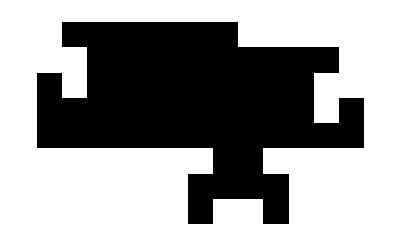

```mathematica
selectedRegion//ArrayPlot
```

```mathematica
n=1;
While[Length[Union[Flatten[ImageData[Dilation[Image[selectedRegion,"Bit"],n]]]]]≠1,n++];
```

```mathematica
n
```

3

```mathematica
Union[Flatten[ImageData[Dilation[Image[selectedRegion,"Bit"],3]]]]
```

{1}

```mathematica
innerBound[usedSpace[space]]
```

3

```mathematica
usedSpace[space]
```

{{0,1,1,1,1,1,1,1,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,1,0},{1,0,1,1,1,1,1,1,1,1,1,0,0},{1,1,1,1,1,1,1,1,1,1,1,0,1},{1,1,1,1,1,1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,1,1,0,0,0,0},{0,0,0,0,0,0,1,1,1,1,0,0,0},{0,0,0,0,0,0,1,0,0,1,0,0,0}}

```mathematica
space//ArrayPlot
```

-Graphics-

```mathematica
scanRange[tile,space]
```

{{1,14},{1,9}}

```mathematica
tile//ArrayPlot
```

-Graphics-

```mathematica
Range[innerBound[usedSpace[space]],14-innerBound[usedSpace[space]]]
```

{3,4,5,6,7,8,9,10,11}

```mathematica
Range[1+innerBound[usedSpace[space]],9-innerBound[usedSpace[space]]-1]
```

{4,5}

```mathematica
SetSharedVariable[minScores];
minScores={};
ParallelMap[
tile=#;
regiontoscan=scanRange[tile,space];
ibound=innerBound[usedSpace[space]];
scores=Transpose[Table[

If[((x≥ (regiontoscan[[1,1]]+ibound) && x≤ (regiontoscan[[1,2]]-ibound))&&(y≥ (regiontoscan[[2,1]]+ibound) && y≤ (regiontoscan[[2,2]]-ibound)))
,score[addTile[tile,space,{x,y}]],Infinity
],
{x,regiontoscan[[1,1]],regiontoscan[[1,2]]},{y,regiontoscan[[2,1]],regiontoscan[[2,2]]}
]];


scoresImg=Transpose[Table[scoreImg[addTile[tile,space,{x,y}]],{x,regiontoscan[[1,1]],regiontoscan[[1,2]]},{y,regiontoscan[[2,1]],regiontoscan[[2,2]]}]];
scores=scores/Max[Cases[{Infinity,1,2,4,10},_Integer]]*(1-scoresImg);
newPos=Reverse[First[Take[Position[scores,Min[scores]],1]]]+First/@regiontoscan-{1,1};
AppendTo[minScores,{Min[scores],addTile[tile,space,newPos]}];
&,tiles];
```

```mathematica
First[SortBy[minScores,#[[1]]&]][[2]]//ArrayPlot
```

-Graphics-

```mathematica
usedSpace[space]//ArrayPlot
```

-Graphics-

```mathematica
innerBound[usedSpace[space]]
```

1

```mathematica
Dimensions[usedSpace[space]]
```

{3,6}

```mathematica
usedRange[space]
```

{{2,7},{2,4}}

```mathematica
space=positionTile[{{1,1,1,0,1,1},{1,1,1,1,1,1},{1,1,1,1,1,0}},{2,2},{10,10}]
```

{{0,0,0,0,0,0,0,0,0,0},{0,1,1,1,0,1,1,0,0,0},{0,1,1,1,1,1,1,0,0,0},{0,1,1,1,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

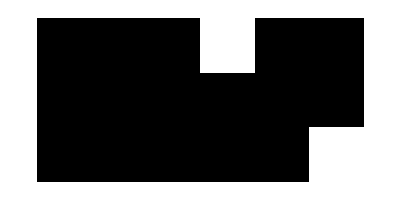
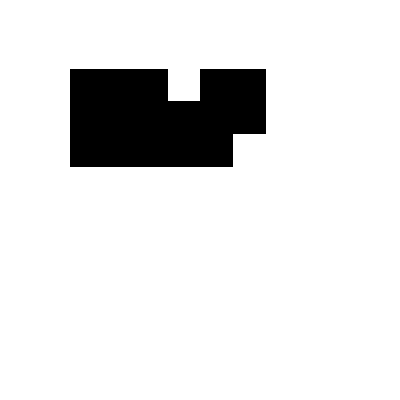

```mathematica
{ArrayPlot[usedSpace[space]],ArrayPlot[space]}
```

```mathematica
spacebak=space
```

{{0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
ClearSystemCache[];
ibound=innerBound[usedSpace[space]];
regiontoscan=scanRange[tile,space];
Transpose[Table[
If[!((x≥ (regiontoscan[[1,1]]+ibound+1) && x≤ (regiontoscan[[1,2]]-ibound-1))&&(y≥ (regiontoscan[[2,1]]+ibound+1) && y≤ (regiontoscan[[2,2]]-ibound-1)))
,scoreImg[addTile[tile,space,{x,y}]],Infinity
],
{x,regiontoscan[[1,1]],regiontoscan[[1,2]]},{y,regiontoscan[[2,1]],regiontoscan[[2,2]]}
]]//TableForm//RepeatedTiming
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

{2.29,0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.662745
0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.678431 | 0.662745
0.552941 | 0.552941 | ∞ | ∞ | ∞ | ∞ | 0.670588 | 0.662745
0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.698039 | 0.666667 | 0.662745
0.682353 | 0.701961 | 0.713725 | 0.705882 | 0.682353 | 0.67451 | 0.662745 | 0.662745}

```mathematica
ClearSystemCache[];
regiontoscan=scanRange[tile,space];
Transpose[Table[scoreImg[addTile[tile,space,{x,y}]],{x,regiontoscan[[1,1]],regiontoscan[[1,2]]},{y,regiontoscan[[2,1]],regiontoscan[[2,2]]}]]//TableForm//RepeatedTiming
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

```mathematica
regiontoscan=scanRange[tile,space]
```

{{1,8},{1,5}}

```mathematica
ibound
```

1

```mathematica
space//ArrayPlot
```

-Graphics-

```mathematica
tile//ArrayPlot
```

-Graphics-

```mathematica
tile={{0,1},{0,1},{1,1}}
```

{{0,1},{0,1},{1,1}}

```mathematica
overlay[space_,{{xmin_,xmax_},{ymin_,ymax_}}]:=Module[{},
temptile=Table[2,{y,ymin,ymax},{x,xmin,xmax}];
ArrayPlot[space+positionTile[temptile,{xmin,ymin},Dimensions[space]]]
]
```

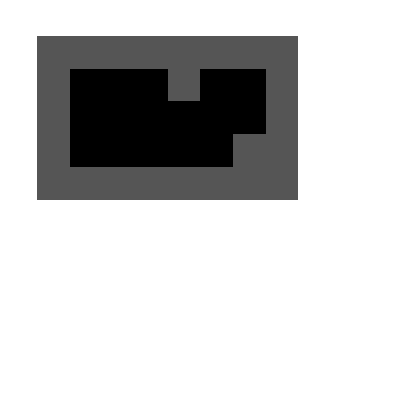

```mathematica
overlay[space,{{1,8},{1,5}}]
```

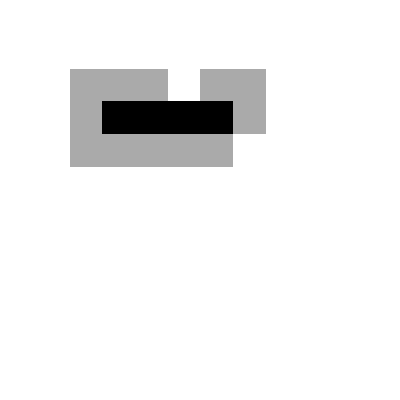

```mathematica
overlay[space,{{3,6},{3,3}}]
```

```mathematica
SetSharedVariable[minScores];
minScores={};
ParallelMap[
tile=#;
regiontoscan=scanRange[tile,space];
ibound=innerBound[usedSpace[space]];
scores=Transpose[Table[scoreImg[addTile[tile,space,{x,y}]],{x,regiontoscan[[1,1]],regiontoscan[[1,2]]},{y,regiontoscan[[2,1]],regiontoscan[[2,2]]}]];
regiontoscan=scanRange[tile,space];
scoresImg=Transpose[Table[
If[!((x≥ (regiontoscan[[1,1]]+ibound+1) && x≤ (regiontoscan[[1,2]]-ibound-1))&&(y≥ (regiontoscan[[2,1]]+ibound+1) && y≤ (regiontoscan[[2,2]]-ibound-1)))
,scoreImg[addTile[tile,space,{x,y}]],0
],
{x,regiontoscan[[1,1]],regiontoscan[[1,2]]},{y,regiontoscan[[2,1]],regiontoscan[[2,2]]}
]];
scores=scores/Max[Cases[{Infinity,1,2,4,10},_Integer]]*(1-scoresImg);
newPos=Reverse[First[Take[Position[scores,Min[scores]],1]]]+First/@regiontoscan-{1,1};
AppendTo[minScores,{Min[scores],addTile[tile,space,newPos]}];
&,tiles];
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

```mathematica
addNextTile[space,tiles]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

{{0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,0,1,1,1,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,0,0,0,0,1,0,1,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,0,0,1,1,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
ArrayPlot[%]
```

-Graphics-

```mathematica
nextSpace={{0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,0,1,1,1,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,0,0,0,0,1,0,1,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,0,0,1,1,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}};
```

```mathematica
nextSpace//ArrayPlot
```

-Graphics-

```mathematica
universe=Table[0,{50},{50}];
```

```mathematica
takeUniverse[space_,{offsetx_,offsety_},{width_,height_}]:=Module[{xRange,yRange,selectedRows},
xRange={offsetx,offsetx+width};
yRange={offsety,offsety+height};
selectedRows=Take[space,yRange];
Map[Take[#,xRange]&,selectedRows]
]
```

```mathematica
space//ArrayPlot
```

-Graphics-

```mathematica
takeUniverse[space,{1,1},{10,12}]//Dimensions
```

{13,11}

```mathematica
putUniverse[universe_,space_,{offsetx_,offsety_}]:=Module[{},
For[j=offsety,j≤ offsety+Dimensions[space][[1]],j++,
universe[[j]][[offsetx;;(offsetx+Dimensions[space][[2]]-1)]]=space[[j]];
]
]
SetAttributes[putUniverse,HoldFirst];
```

```mathematica
space
```

```mathematica
space[[1;;2]]={{0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}
```

{{0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
universe;
```

```mathematica
space
```

```mathematica
putUniverse[universe,{{1,1},{1,1}},{1,1}]
```

Part::partw: Part 3 of {{1,1},{1,1}} does not exist.

```mathematica
space[[1]]
```

{0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
universe=Table[0,{50},{50}];
```

```mathematica
Dimensions[space]
```

{20,20}

```mathematica
space=Table[Round[RandomReal[]],{10},{12}]
```

{{0,1,0,1,0,1,1,0,1,1,1,0},{0,1,1,0,1,0,1,1,1,0,1,0},{0,1,0,1,0,0,0,0,0,0,1,1},{0,1,0,1,0,1,0,0,1,0,0,1},{0,0,1,1,1,0,1,1,1,1,0,1},{0,1,1,0,0,0,1,0,0,1,0,1},{0,0,1,1,1,1,1,1,0,0,1,1},{0,1,0,0,0,1,0,1,1,0,1,0},{0,1,1,1,0,0,0,0,0,1,1,1},{1,0,1,0,1,1,0,0,0,1,1,1}}

```mathematica
Dimensions[space]
```

{10,12}

```mathematica
universe[[1]][[4;;15]]=space[[1]]
```

{0,1,0,1,0,1,1,0,1,1,1,1}

```mathematica
universe//ArrayPlot
```

-Graphics-

```mathematica
takeUniverse[universe,{1,1},{10,10}]
```

{{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
putUniverse[universe,space,{1,1}]
```

```mathematica
universe//ArrayPlot
```

-Graphics-

```mathematica
space//ArrayPlot
```

-Graphics-

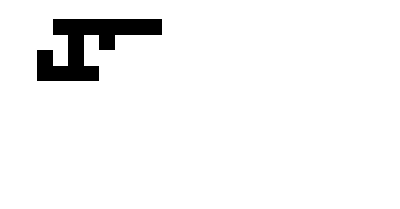

```mathematica
takeUniverse[universe,{1,1},{20,10}]//ArrayPlot
```

```mathematica
space=takeUniverse[universe,{1,1},{20,10}]
```

{{0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
space=increaseSpace[space,3,10]
```

{{0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
space//ArrayPlot
```

-Graphics-

```mathematica
addNextTile[space,tiles]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

{{0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{1,0,1,1,1,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,0,0,1,1,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
space=%
```

{{0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{1,0,1,1,1,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,0,0,1,1,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
space//ArrayPlot
```

-Graphics-

```mathematica
space=addNextTile[space,tiles]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

{{0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
space//ArrayPlot
```

-Graphics-

```mathematica
space=addNextTile[space,tiles]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

{{0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
space//ArrayPlot
```

-Graphics-

```mathematica
space=addNextTile[space,tiles]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

{{0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
space//ArrayPlot
```

-Graphics-

```mathematica
space=addNextTile[space,tiles]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

{{0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,1,1,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
%//ArrayPlot
```

-Graphics-

```mathematica
Tally[Flatten[space]][[2,2]]/Tally[Flatten[space]][[1,2]]//N
```

0.431818

```mathematica
usedRange[space]
```

{{1,13},{1,14}}

```mathematica
usedRange[space][[2,2]]/Dimensions[space][[2]]//N
```

0.666667

```mathematica
If[usedRange[space][[2,2]]/Dimensions[space][[2]]>0.5,
putUniverse[universe,space,{1,1}]
]
```

```mathematica
Last/@Dimensions/@tiles//Max
```

13

```mathematica
space=takeUniverse[universe,{1,2},{20,20}]
```

{{0,0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,1,1,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
space//ArrayPlot
```

-Graphics-

```mathematica
space=addNextTile[space,tiles]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

{{0,0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,1,1,0,1,1,1,1,0,1,0,0,0,0,0,0,0,0},{1,0,1,0,0,0,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0},{1,1,1,1,0,0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
space=addNextTile[space,tiles]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

{{0,0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
innerBound[usedSpace[space]]
```

3

```mathematica
putUniverse[universe,space,{1,2}]
```

```mathematica
universe//ArrayPlot
```

-Graphics-

```mathematica
takeUniverse[universe,{1,4},{20,20}]//ArrayPlot
```

-Graphics-

```mathematica
space=takeUniverse[universe,{1,4},{20,20}]
```

{{1,1,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
addNextTile[space,tiles]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

{{1,1,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
ArrayPlot[%]
```

-Graphics-

```mathematica
space={{1,1,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}};
```

```mathematica
putUniverse[universe,space,{1,4}]
```

```mathematica
universe//ArrayPlot
```

-Graphics-

```mathematica
usedRange[universe]
```

{{1,16},{1,18}}

```mathematica
innerBound[universe]
```

3

```mathematica
takeUniverse[universe,{1,18-3},{20,20}]//ArrayPlot
```

-Graphics-

```mathematica
space=takeUniverse[universe,{1,18-3},{20,20}]
```

{{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
addNextTile[space,tiles]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

{{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
ArrayPlot[%]
```

-Graphics-

```mathematica
space={{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}};
```

```mathematica
addNextTile[space,tiles]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

{{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,0,0,1,1,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
ArrayPlot[%]
```

-Graphics-

```mathematica
putUniverse[universe,space,{1,15}]
```

```mathematica
universe//ArrayPlot
```

-Graphics-

```mathematica
innerBound[universe]
```

5

```mathematica
usedRange[universe]
```

{{1,16},{1,19}}

```mathematica
overlay[universe,{{1,20},{19-5,19-5+20}}]
```

-Graphics-

```mathematica
takeUniverse[universe,{1,19-5},{19,19}]//ArrayPlot
```

-Graphics-

```mathematica
space=takeUniverse[universe,{1,19-5},{19,19}]
```

{{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
addNextTile[space,tiles]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

{{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{0,0,0,1,0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{0,0,0,1,1,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0,1,0,1,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,0,0,1,1,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
space={{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{0,0,0,1,0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{0,0,0,1,1,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0,1,0,1,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,0,0,1,1,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}};
```

```mathematica
ArrayPlot[space]
```

-Graphics-

```mathematica
putUniverse[universe,space,{1,19-5}]
```

-Graphics-

```mathematica
innerBound[universe]
```

5

```mathematica
usedRange[universe]
```

{{1,16},{1,23}}

```mathematica
overlay[universe,{{5,11},{5,18}}]
```

-Graphics-

```mathematica
First/@Dimensions/@tiles//Max
```

13

```mathematica
universeBackup=universe;
```

```mathematica
growDownStep[universe_,tiles_]:=Module[{usedrange,ibound},
universeBackup=universe;
dimension=Ceiling[1.5*(First/@Dimensions/@tiles//Max)];
usedrange=usedRange[universe];
ibound=innerBound[universe];
spaced=takeUniverse[universe,{1,usedrange[[2,2]]-ibound},{dimension,dimension}];
spaced=addNextTile[spaced,tiles];
putUniverse[universe,spaced,{1,usedrange[[2,2]]-ibound}]
]
```

```mathematica
growDownStep[universe,tiles]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

-Graphics-

```mathematica
ibound=innerBound[universe]
```

5

```mathematica
range=usedRange[universe]
```

{{1,16},{1,27}}

```mathematica
overlay[universe,{{6,11},{6,22}}]
```

-Graphics-

```mathematica
Transpose[Table[If[!((x≥ (range[[1,1]]+ibound+1) && x≤ (range[[1,2]]-ibound-1))&&(y≥ (range[[2,1]]+ibound+1) && y≤ (range[[2,2]]-ibound-1)))
,1,0
],{x,range[[1,1]],range[[1,2]]},{y,range[[2,1]],range[[2,2]]}]]
```

{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,0,0,0,0,1,1,1,1,1,1},{1,1,1,1,1,1,0,0,0,0,1,1,1,1,1,1},{1,1,1,1,1,1,0,0,0,0,1,1,1,1,1,1},{1,1,1,1,1,1,0,0,0,0,1,1,1,1,1,1},{1,1,1,1,1,1,0,0,0,0,1,1,1,1,1,1},{1,1,1,1,1,1,0,0,0,0,1,1,1,1,1,1},{1,1,1,1,1,1,0,0,0,0,1,1,1,1,1,1},{1,1,1,1,1,1,0,0,0,0,1,1,1,1,1,1},{1,1,1,1,1,1,0,0,0,0,1,1,1,1,1,1},{1,1,1,1,1,1,0,0,0,0,1,1,1,1,1,1},{1,1,1,1,1,1,0,0,0,0,1,1,1,1,1,1},{1,1,1,1,1,1,0,0,0,0,1,1,1,1,1,1},{1,1,1,1,1,1,0,0,0,0,1,1,1,1,1,1},{1,1,1,1,1,1,0,0,0,0,1,1,1,1,1,1},{1,1,1,1,1,1,0,0,0,0,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}

```mathematica
irange={{6,11},{6,22}}
```

{{6,11},{6,22}}

```mathematica
Join[Table[{11,y},{y,1,18}],Table[{x,22},{x,1,7}]]
```

{{11,1},{11,2},{11,3},{11,4},{11,5},{11,6},{11,7},{11,8},{11,9},{11,10},{11,11},{11,12},{11,13},{11,14},{11,15},{11,16},{11,17},{11,18},{1,22},{2,22},{3,22},{4,22},{5,22},{6,22},{7,22}}

```mathematica
growDownStep[universe_,tiles_]:=Module[{usedrange,ibound},
universeBackup=universe;
dimension=Ceiling[1.5*(First/@Dimensions/@tiles//Max)];
usedrange=usedRange[universe];
ibound=innerBound[universe];
spaced=takeUniverse[universe,{1,usedrange[[2,2]]-ibound},{dimension,dimension}];
spaced=addNextTile[spaced,tiles];
putUniverse[universe,spaced,{1,usedrange[[2,2]]-ibound}]
]
```

```mathematica
Map[
addNextTile[#,tiles]&,

Take[Map[takeUniverse[universe,#,{dimension,dimension}]&,Join[Table[{8,y},{y,1,18,4}],Table[{x,22},{x,1,7,4}]]],3]
]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

{{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}}

```mathematica
Map[ArrayPlot,%]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[ArrayPlot,%]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
growDownStep[universe,tiles]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

-Graphics-

```mathematica
growDownStep[universe,tiles]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

-Graphics-

```mathematica
growDownStep[universe,tiles,5]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

-Graphics-

```mathematica
overlay[universe,{{5,25},{1,20}}]
```

-Graphics-

```mathematica
spaced//ArrayPlot
```

-Graphics-

```mathematica
growSideStep[universe,tiles]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

-Graphics-

```mathematica
universe//ArrayPlot
```

-Graphics-

```mathematica
growSideStep[universe,tiles]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

-Graphics-

```mathematica
universe=universeBackup;
```

```mathematica
innerBound[universe]
```

5

```mathematica
growSideStep[universe,tiles,1]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

-Graphics-

```mathematica
regiontoscan
```

0

```mathematica
offsetx=1
```

1

```mathematica
universeBackup=universe;
dimension=Ceiling[1.5*(First/@Dimensions/@tiles//Max)];
usedrange=usedRange[universe];
ibound=innerBound[universe];
spaced=takeUniverse[universe,{offsetx,usedrange[[2,2]]-ibound},{dimension,dimension}];
```

```mathematica
space=spaced
```

{{0,0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,1,1,0,1,1,1,1,0,1,0,0,0,0,0,0,0,0},{1,0,1,0,0,0,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0},{1,1,1,1,0,0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
universe//ArrayPlot
```

-Graphics-

```mathematica
addNextTile[universe,tiles]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

$Aborted

```mathematica
dimension=Ceiling[1.5*(First/@Dimensions/@tiles//Max)];
```

```mathematica
usedrange=usedRange[universe];
```

```mathematica
ibound=innerBound[universe];
```

```mathematica
spaced=takeUniverse[universe,{usedrange[[1,2]]-ibound-2,1},{dimension,dimension}];
```

```mathematica
spaced//ArrayPlot
```

-Graphics-

```mathematica
SetSharedVariable[minScores];
```

```mathematica
minScores={};
```

```mathematica
tile=tiles[[9]]
```

{{1,0,0,1},{1,1,1,1},{0,1,1,0},{0,1,1,0},{1,1,1,1},{1,0,0,1}}

```mathematica
regiontoscan=scanRange[tile,space];
```

```mathematica
regiontoscan
```

{{1,17},{1,7}}

```mathematica
overlay[spaced,scanRange[tile,spaced]]
```

-Graphics-

```mathematica
regiontoscan=scanRange[tile,spaced]
```

{{1,9},{1,16}}

```mathematica
scores=Transpose[Table[score[addTile[tile,spaced,{x,y}]],{x,regiontoscan[[1,1]],regiontoscan[[1,2]]},{y,regiontoscan[[2,1]],regiontoscan[[2,2]]}]];
```

```mathematica
scores//MatrixForm
```

(∞ | ∞ | ∞ | ∞ | ∞ | 189 | 210 | 231 | 252
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 200 | 220 | 240
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 200 | 220 | 240
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 200 | 220 | 240
∞ | ∞ | ∞ | ∞ | ∞ | 180 | 200 | 220 | 240
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 200 | 220 | 240
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 200 | 220 | 240
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 240
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 240
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 220 | 240
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 240
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 240
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 240
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 240
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 200 | ∞ | 240
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 240)

```mathematica
scoresImg=Transpose[Table[scoreImg[addTile[tile,spaced,{x,y}]],{x,regiontoscan[[1,1]],regiontoscan[[1,2]]},{y,regiontoscan[[2,1]],regiontoscan[[2,2]]}]];
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

```mathematica
scoresImg//MatrixForm
```

(0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.643137 | 0.643137 | 0.643137 | 0.643137
0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.643137 | 0.643137 | 0.643137 | 0.643137
0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.643137 | 0.643137 | 0.643137 | 0.643137
0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.643137 | 0.643137 | 0.643137 | 0.643137
0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.647059 | 0.643137 | 0.643137 | 0.643137
0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.654902 | 0.647059 | 0.647059 | 0.643137
0.552941 | 0.552941 | 0.552941 | 0.701961 | 0.552941 | 0.666667 | 0.65098 | 0.647059 | 0.647059
0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.647059
0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.65098
0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.666667 | 0.65098
0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.670588 | 0.654902
0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.658824
0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.658824
0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.682353 | 0.658824
0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.717647 | 0.682353 | 0.658824
0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.552941 | 0.682353 | 0.658824)

```mathematica
scores=scores/Max[Cases[Flatten[scores],_Integer]]*(1-scoresImg);
```

```mathematica
180*(1-0.5529411764705883)
```

80.4706

```mathematica
Max[Cases[{Infinity,1,2,4,10},_Integer]]
```

10

```mathematica
scores//MatrixForm
```

(∞ | ∞ | ∞ | ∞ | ∞ | 0.267647 | 0.297386 | 0.327124 | 0.356863
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0.283224 | 0.311547 | 0.339869
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0.283224 | 0.311547 | 0.339869
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0.283224 | 0.311547 | 0.339869
∞ | ∞ | ∞ | ∞ | ∞ | 0.252101 | 0.283224 | 0.311547 | 0.339869
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0.280112 | 0.308123 | 0.339869
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0.277 | 0.308123 | 0.336134
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0.336134
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0.3324
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0.291005 | 0.3324
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0.328665
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0.32493
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0.32493
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0.32493
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0.22409 | ∞ | 0.32493
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0.32493)

```mathematica
growSideStep[universe,tiles,1]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

-Graphics-

```mathematica
universe=universeBackup;
```

```mathematica
ArrayPlot[universe]
```

-Graphics-

```mathematica
dimension=Ceiling[1.5*(First/@Dimensions/@tiles//Max)];
```

```mathematica
usedrange=usedRange[universe];
```

```mathematica
usedrange
```

{{1,16},{1,32}}

```mathematica
ibound=innerBound[universe];
```

```mathematica
spaced=takeUniverse[universe,{usedrange[[1,2]]-ibound-2,1},{dimension,dimension}];
```

```mathematica
spaced//ArrayPlot
```

-Graphics-

```mathematica
addNextTile[spaced,tiles]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
ArrayPlot[%]
```

-Graphics-

```mathematica
tile=tiles[[9]]
```

{{1,0,0,1},{1,1,1,1},{0,1,1,0},{0,1,1,0},{1,1,1,1},{1,0,0,1}}

```mathematica
tile//ArrayPlot
```

-Graphics-

```mathematica
SetSharedVariable[minScores];
minScores={};
```

```mathematica
regiontoscan=scanRange[tile,spaced]
```

{{1,9},{1,16}}

```mathematica
overlay[spaced,{{1,5},{1,6}}]
```

-Graphics-

```mathematica
scores=Transpose[Table[score[addTile[tile,spaced,{x,y}]],{x,regiontoscan[[1,1]],regiontoscan[[1,2]]},{y,regiontoscan[[2,1]],regiontoscan[[2,2]]}]];
```

```mathematica
scores//MatrixForm
```

(∞ | ∞ | ∞ | ∞ | ∞ | 189 | 210 | 231 | 252
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 200 | 220 | 240
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 200 | 220 | 240
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 200 | 220 | 240
∞ | ∞ | ∞ | ∞ | ∞ | 180 | 200 | 220 | 240
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 200 | 220 | 240
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 200 | 220 | 240
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 240
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 240
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 220 | 240
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 240
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 240
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 240
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 240
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 200 | ∞ | 240
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 240)

```mathematica
newPos=Reverse[First[Take[Position[scores,Min[scores]],1]]]+First/@regiontoscan-{1,1};
```

```mathematica
newPos
```

{6,5}

```mathematica
AppendTo[minScores,{Min[scores],addTile[tile,spaced,newPos]}];
&,tiles];
```

```mathematica
addTile[tile,spaced,newPos]//ArrayPlot
```

-Graphics-

```mathematica
universe//ArrayPlot
```

-Graphics-

```mathematica
universeStart=universe;
```

```mathematica
growSideStep[universe,tiles]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

-Graphics-

```mathematica
universe//ArrayPlot
```

-Graphics-

```mathematica
space
```

0

```mathematica
universe//ArrayPlot
```

-Graphics-

```mathematica
putUniverse[universe,space,{1,1}]
```

-Graphics-

```mathematica
growDownStep[universe,tiles,1]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

-Graphics-

```mathematica
universe//ArrayPlot
```

```mathematica
universeBackup=universe;
```

```mathematica
dimension=Ceiling[1.5*(First/@Dimensions/@tiles//Max)];
```

```mathematica
usedrange=usedRange[universe];
```

```mathematica
usedrange
```

{{1,8},{1,4}}

```mathematica
ibound=innerBound[universe];
```

```mathematica
innerBound[universe]
```

```mathematica
ibound
```

2

```mathematica
usedSpace[universe]//ArrayPlot
```

-Graphics-

```mathematica
n=2;
```

```mathematica
{Drop[Drop[Map[Drop[Drop[#,n],-n]&,usedSpace[universe]],n],-n]//ArrayPlot,Length[Union[Flatten[Drop[Drop[Map[Drop[Drop[#,n],-n]&,usedSpace[universe]],n],-n]]]]}
```

{-Graphics-,0}

```mathematica
innerBound[universe]
```

2

```mathematica
space//ArrayPlot
```

-Graphics-

```mathematica
addNextTile[space,tiles]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

{{0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,0,1,1,1,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,0,0,0,0,1,0,1,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,0,0,1,1,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
ArrayPlot[{{0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,0,1,1,1,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,0,0,0,0,1,0,1,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,0,0,1,1,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}]
```

-Graphics-

```mathematica
putUniverse[universe,{{0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,0,1,1,1,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,0,0,0,0,1,0,1,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,0,0,1,1,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{1,1}]
```

-Graphics-

```mathematica
universeBackup=universe;
```

```mathematica
dimension=Ceiling[1.5*(First/@Dimensions/@tiles//Max)];
```

```mathematica
usedrange=usedRange[universe];
```

```mathematica
usedrange
```

{{1,13},{1,5}}

```mathematica
ibound=innerBound[universe]
```

3

```mathematica
n=3
```

3

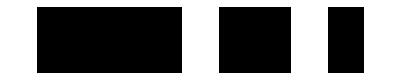

```mathematica
Drop[Drop[Map[Drop[Drop[#,2],-2]&,usedSpace[universe]],2],-2]//ArrayPlot
```

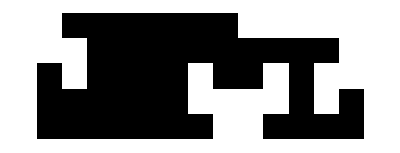

```mathematica
usedSpace[universe]//ArrayPlot
```

```mathematica
innerBound[universe]
```

Drop::drop: Cannot drop positions -3 through -1 in {{1,1,1,0,0,0,0},{1,1,1,1,0,0,1}}.

Drop::normal: Nonatomic expression expected at position 1 in Drop[-3,{{1,1,1,0,0,0,0},{1,1,1,1,0,0,1}}].

Drop::drop: Cannot drop positions -4 through -1 in {{1,1,1,0,0}}.

Drop::normal: Nonatomic expression expected at position 1 in Drop[-4,{{1,1,1,0,0}}].

Drop::drop: Cannot drop positions -5 through -1 in {}.

General::stop: Further output of Drop::drop will be suppressed during this calculation.

Drop::normal: Nonatomic expression expected at position 1 in Drop[-5,{}].

General::stop: Further output of Drop::normal will be suppressed during this calculation.

25

```mathematica
Min[Dimensions[universe]]
```

50

```mathematica
innerBound[universe]
```

2

```mathematica
addNextTile[universe,tiles]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

$Aborted

```mathematica
addNextTile[space,tiles]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

$Aborted

```mathematica
universe//ArrayPlot
```

-Graphics-

```mathematica
universeBackup=universe;
```

```mathematica
dimension=Ceiling[1.5*(First/@Dimensions/@tiles//Max)];
```

```mathematica
usedrange=usedRange[universe];
```

```mathematica
ibound=innerBound[universe];
```

```mathematica
spaced=takeUniverse[universe,{offsetx,usedrange[[2,2]]-ibound},{dimension,dimension}];
```

```mathematica
spaced//ArrayPlot
```

-Graphics-

```mathematica
spaced=addNextTile[spaced,tiles];
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

```mathematica
putUniverse[universe,spaced,{offsetx,usedrange[[2,2]]-ibound}]
```

-Graphics-

```mathematica
universe//ArrayPlot
```

-Graphics-

```mathematica
growDownStep[universe,tiles]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

-Graphics-

```mathematica
growDownStep[universe,tiles]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

-Graphics-

```mathematica
growDownStep[universe,tiles]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

-Graphics-

```mathematica
universe//ArrayPlot
```

-Graphics-

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

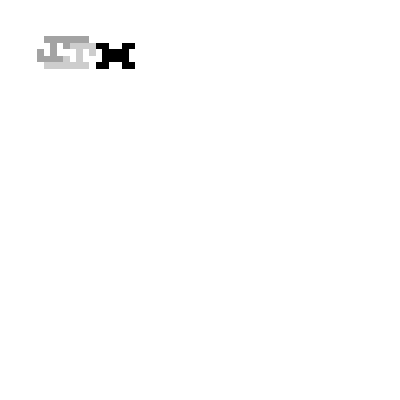

```mathematica
growDownStep[universe,tiles,1]
```

```mathematica
;
visualUniverse=visualUniverse+(RandomReal[])*(universe-universeBackup);
ArrayPlot[visualUniverse]
```

```mathematica
universeBackup=universe;
```

```mathematica
dimension=Ceiling[1.5*(First/@Dimensions/@tiles//Max)];
```

```mathematica
usedrange=usedRange[universe]
```

{{1,8},{1,4}}

```mathematica
ibound=innerBound[universe]
```

2

```mathematica
spaced=takeUniverse[universe,{1,1},{dimension,dimension}];
spaced//ArrayPlot
```

-Graphics-

```mathematica
innerBound[universe]
```

2

```mathematica
usedSpace[universe]//ArrayPlot
```

-Graphics-

```mathematica
Max[Map[distanceFromBoundary[#,Dimensions[usedSpace[universe]]]&,Position[usedSpace[universe],0]]]
```

4

```mathematica
distanceFromBoundary[point_,dimension_]:=Module[{x,y},
x=0;
y=0;
If[point[[1]]≥dimension[[1]]/2,
x=dimension[[1]]-point[[1]];,
x=point[[1]];
];
If[point[[2]]≥dimension[[2]]/2,
x=dimension[[2]]-point[[2]];,
x=point[[2]];
];
Max[x,y]
];
```

```mathematica
innerBound[universe]
```

4

```mathematica
universe//ArrayPlot
```

-Graphics-

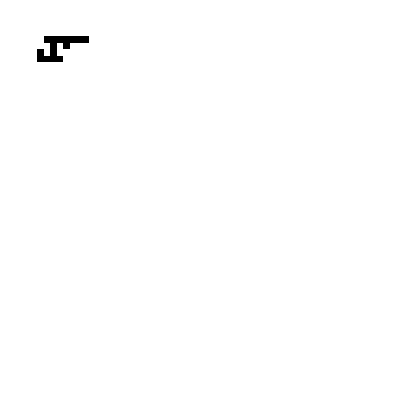

```mathematica
visualUniverse//ArrayPlot
```

```mathematica
space//ArrayPlot
```

-Graphics-

```mathematica
addNextTile[space,tiles]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

{{0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,0,1,1,1,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,0,0,0,0,1,0,1,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,0,0,1,1,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
ArrayPlot[%]
```

-Graphics-

```mathematica
universe//ArrayPlot
```

-Graphics-

```mathematica
space
```

{{0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
positionTile[tile]
```

positionTile[{{1,1,1},{1,0,0}}]

```mathematica
space2//ArrayPlot
```

-Graphics-

```mathematica
space//ArrayPlot
```

-Graphics-

```mathematica
space={{0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,0,1,1,1,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,0,0,0,0,1,0,1,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,0,0,1,1,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}
```

{{0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,0,1,1,1,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,0,0,0,0,1,0,1,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,0,0,1,1,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
space//ArrayPlot
```

-Graphics-

```mathematica
space2//ArrayPlot
```

-Graphics-

```mathematica
visualSpace=Table[0,{20},{20}];
visualSpace=space2;
```

```mathematica
visualSpace=visualSpace+RandomReal[]*(space-space2)
```

{{0.,1.,1.,1.,1.,1.,1.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,1.,0.673532,1.,0.673532,0.673532,0.673532,0.673532,0.673532,0.673532,0.673532,0.,0.,0.,0.,0.,0.,0.,0.},{1.,0.,1.,0.673532,0.673532,0.673532,0.,0.673532,0.673532,0.,0.673532,0.,0.,0.,0.,0.,0.,0.,0.,0.},{1.,1.,1.,1.,0.673532,0.673532,0.,0.,0.,0.,0.673532,0.,0.673532,0.,0.,0.,0.,0.,0.,0.},{0.673532,0.673532,0.673532,0.673532,0.673532,0.673532,0.673532,0.,0.,0.673532,0.673532,0.673532,0.673532,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

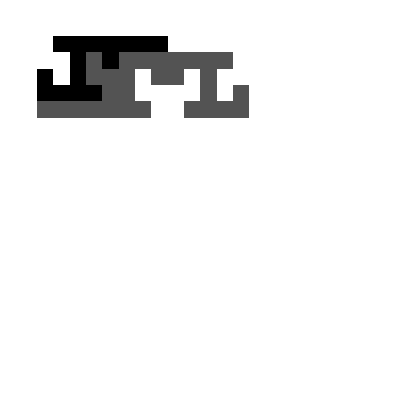

```mathematica
visualSpace//ArrayPlot
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

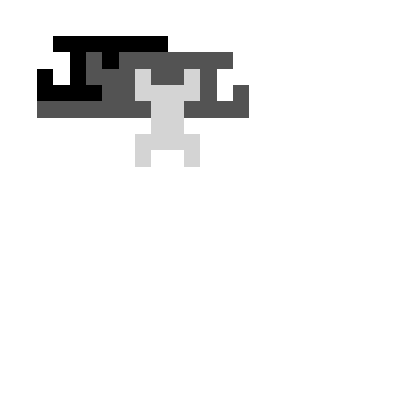

```mathematica
space2=space;
space=addNextTile[space,tiles];
visualSpace=visualSpace+RandomReal[]*(space-space2);
ArrayPlot[visualSpace]
```

```mathematica
space//ArrayPlot
```

-Graphics-

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

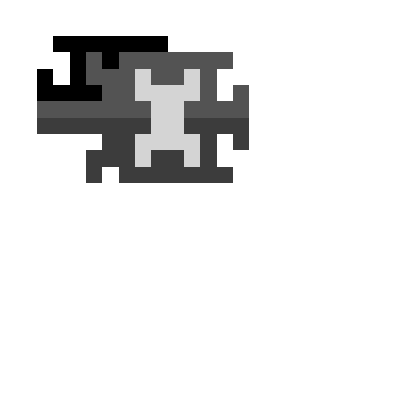

```mathematica
addNextTileLocal[]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

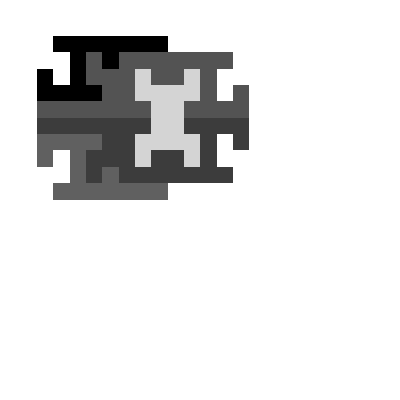

```mathematica
addNextTileLocal[]
```

```mathematica
putUniverse[universe,space,{1,1}]
```

-Graphics-

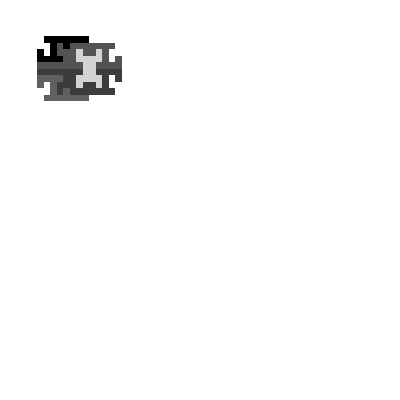

```mathematica
putUniverse[visualUniverse,visualSpace,{1,1}]
```

```mathematica
growDownStep[universe,tiles,1]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

-Graphics-

```mathematica
universe=universeBackup;
```

```mathematica
growDownStep[universe,tiles,1]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

-Graphics-

```mathematica
visualUniverse//ArrayPlot
```

-Graphics-

```mathematica
universe//ArrayPlot
```

-Graphics-

```mathematica
universe=universeBackup;
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

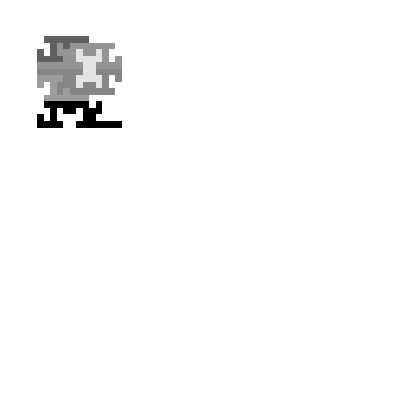

```mathematica
growDownStep[universe,tiles,1]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

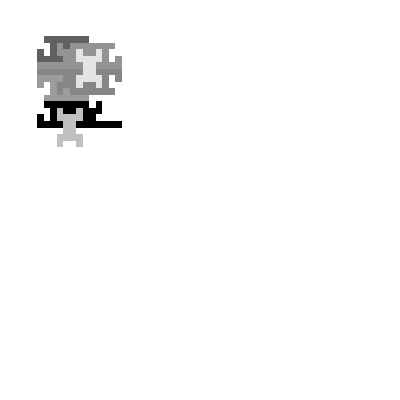

```mathematica
growDownStep[universe,tiles,1]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

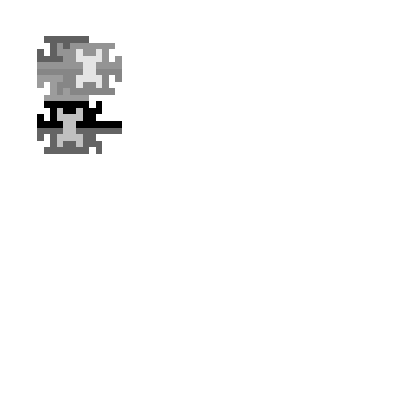

```mathematica
growDownStep[universe,tiles,1]
```

```mathematica
universe2=universe;
visualUniverse2=visualUniverse;
```

```mathematica
growSideStep[universe2,tiles,1,visualUniverse2]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

Set::setraw: Cannot assign to raw object {{0.,1.,1.,1.,1.,1.,1.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},«48»,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}.

-Graphics-

```mathematica
universe//ArrayPlot
```

-Graphics-

```mathematica
universeBackup=universe;
```

```mathematica
dimension=Ceiling[1.5*(First/@Dimensions/@tiles//Max)];
```

```mathematica
usedrange=usedRange[universe];
```

```mathematica
ibound=innerBound[universe];
```

```mathematica
ibound
```

4

```mathematica
spaced=takeUniverse[universe,{usedrange[[1,2]]-ibound,1},{dimension,dimension}];
```

```mathematica
spaced//ArrayPlot
```

-Graphics-

```mathematica
spaced=addNextTile[spaced,tiles];
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

```mathematica
spaced//ArrayPlot
```

-Graphics-

```mathematica
growSideStep[universe,tiles]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

-Graphics-

```mathematica
universe//ArrayPlot
```

-Graphics-

```mathematica
universeBackup//ArrayPlot
```

-Graphics-

```mathematica
universe=universeBackup;
```

```mathematica
growSideStep[universe,tiles,1, visualUniverse]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

Set::setraw: Cannot assign to raw object {{0.,1.,1.,1.,1.,1.,1.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},«48»,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}.

-Graphics-

```mathematica
universeBackup=universe;
```

```mathematica
dimension=Ceiling[1.5*(First/@Dimensions/@tiles//Max)];
```

```mathematica
usedrange=usedRange[universe];
ibound=innerBound[universe];
```

```mathematica
spaced=takeUniverse[universe,{usedrange[[1,2]]-ibound,1},{dimension,dimension}];
spaced=addNextTile[spaced,tiles];
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

```mathematica
spaced//ArrayPlot
```

-Graphics-

```mathematica
putUniverse[universe,spaced,{usedrange[[1,2]]-ibound,1}];
```

```mathematica
visualUniverse=visualUniverse+RandomReal[]*(universe-universeBackup);
```

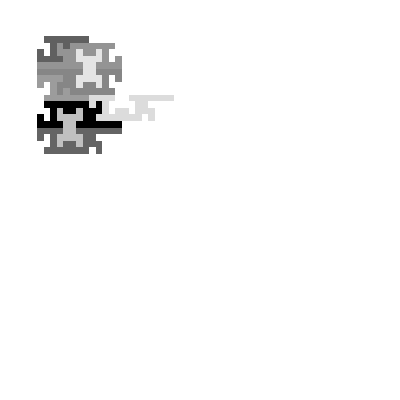

```mathematica
visualUniverse//ArrayPlot
```

```mathematica
ArrayPlot[visualUniverse]
```

-Graphics-

```mathematica
growSideStep[universe,tiles,1,visualUniverse]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

Set::setraw: Cannot assign to raw object {{0.,1.,1.,1.,1.,1.,1.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},«48»,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}.

-Graphics-

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

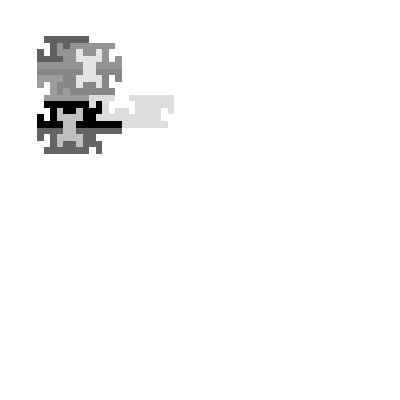

```mathematica
universeBackup=universe;
dimension=Ceiling[1.5*(First/@Dimensions/@tiles//Max)];
usedrange=usedRange[universe];
ibound=innerBound[universe];
spaced=takeUniverse[universe,{usedrange[[1,2]]-ibound,1},{dimension,dimension}];
spaced=addNextTile[spaced,tiles];
putUniverse[universe,spaced,{usedrange[[1,2]]-ibound,1}];
visualUniverse=visualUniverse+RandomReal[]*(universe-universeBackup);ArrayPlot[visualUniverse]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

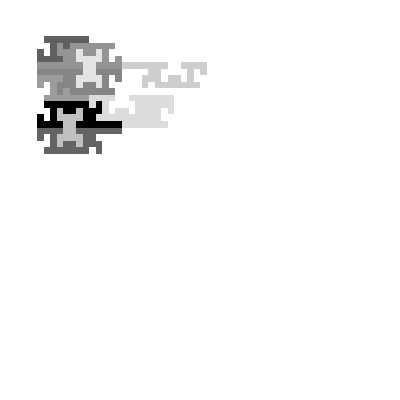

```mathematica
growSideStep[universe,tiles,1,visualUniverse]
```

```mathematica
universe=universeBackup;
```

```mathematica
universeBackup1=universeBackup;
```

```mathematica
space//ArrayPlot
```

-Graphics-

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

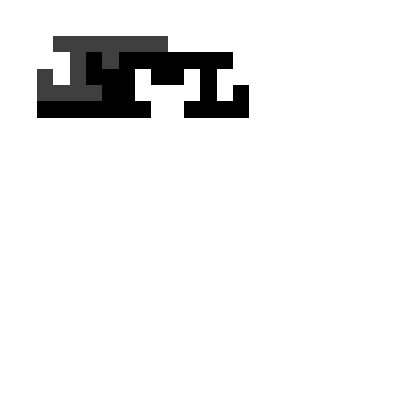

```mathematica
addNextTileLocal[]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

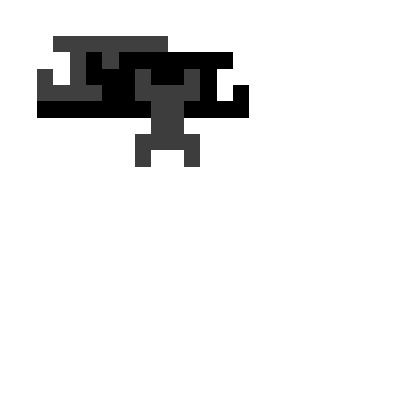

```mathematica
addNextTileLocal[]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

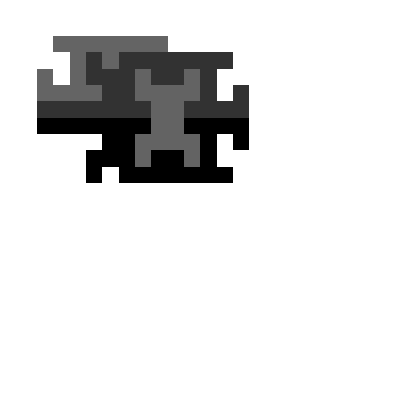

```mathematica
addNextTileLocal[]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

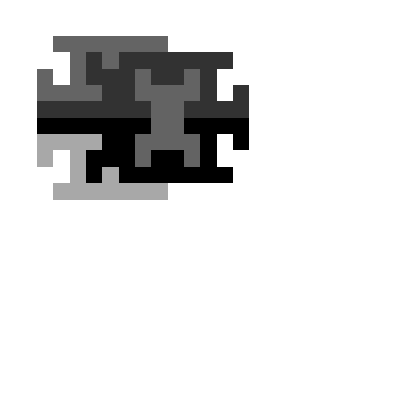

```mathematica
addNextTileLocal[]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

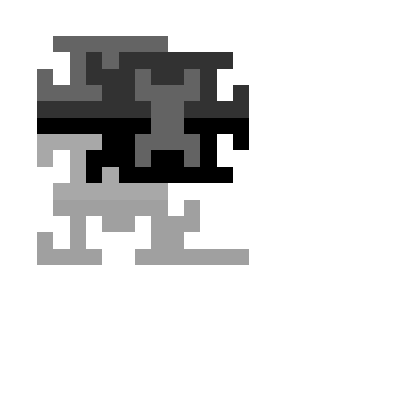

```mathematica
addNextTileLocal[]
```

```mathematica
tile=tiles[[9]];
regiontoscan=scanRange[tile,space];
scores=Transpose[Table[score[addTile[tile,space,{x,y}]],{x,regiontoscan[[1,1]],regiontoscan[[1,2]]},{y,regiontoscan[[2,1]],regiontoscan[[2,2]]}]];
scoresImg=Transpose[Table[scoreImg[addTile[tile,space,{x,y}]],{x,regiontoscan[[1,1]],regiontoscan[[1,2]]},{y,regiontoscan[[2,1]],regiontoscan[[2,2]]}]];
scores=scores/Max[Cases[{Infinity,1,2,4,10},_Integer]]*(1-scoresImg)
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

{{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,1.49333},{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞},{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞},{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞},{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,1.49333},{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,1.49333},{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,1.23529,∞,1.49333},{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞},{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,1.49333},{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,1.6},{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,1.60627,1.70667},{∞,∞,∞,1.3,∞,∞,∞,∞,∞,∞,∞,∞,1.70667,1.81333},{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,1.92},{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,2.02667},{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,1.88235,2.00784,2.13333}}

```mathematica
MatrixForm[%]
```

(∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1.49333
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1.49333
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1.49333
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1.23529 | ∞ | 1.49333
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1.49333
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1.6
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1.60627 | 1.70667
∞ | ∞ | ∞ | 1.3 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1.70667 | 1.81333
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1.92
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2.02667
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1.88235 | 2.00784 | 2.13333)

```mathematica
cost={{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,1.4933333333333334},{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞},{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞},{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞},{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,1.4933333333333334},{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,1.4933333333333334},{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,1.235294117647059,∞,1.4933333333333334},{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞},{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,1.4933333333333334},{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,1.6},{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,1.6062745098039217,1.7066666666666666},{∞,∞,∞,1.3000000000000003,∞,∞,∞,∞,∞,∞,∞,∞,1.7066666666666666,1.8133333333333332},{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,1.9200000000000002},{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,2.0266666666666664},{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,1.8823529411764706,2.007843137254902,2.1333333333333333}}
```

{{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,1.49333},{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞},{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞},{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞},{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,1.49333},{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,1.49333},{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,1.23529,∞,1.49333},{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞},{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,1.49333},{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,1.6},{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,1.60627,1.70667},{∞,∞,∞,1.3,∞,∞,∞,∞,∞,∞,∞,∞,1.70667,1.81333},{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,1.92},{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,2.02667},{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,1.88235,2.00784,2.13333}}

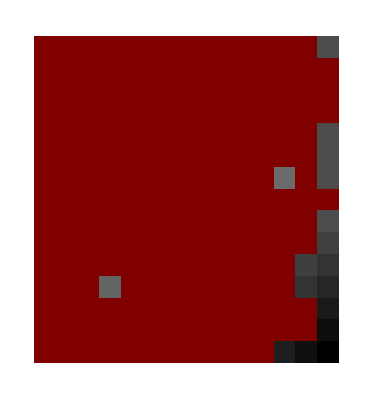

```mathematica
ArrayPlot[cost]
```

```mathematica
switchToUniversal[]
```

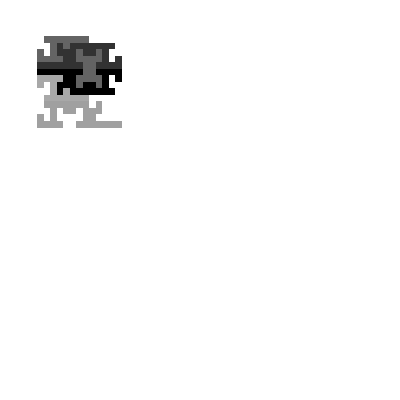

```mathematica
visualUniverse//ArrayPlot
```

```mathematica
overlay[universe,{{1,20},{1,20}}]
```

-Graphics-

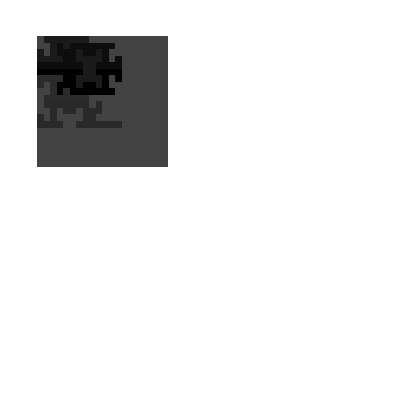

```mathematica
overlay[visualUniverse,{{1,20},{1,20}}]
```

```mathematica
space//ArrayPlot
```

-Graphics-

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

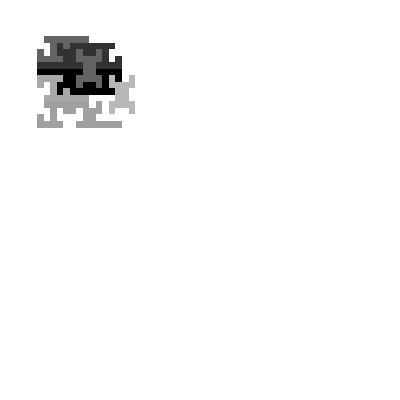

```mathematica
growSideStep[universe,tiles,1,visualUniverse]
```

```mathematica
overlay[universe,{{usedrange[[1,2]]-ibound,usedrange[[1,2]]-ibound+20},{1,1+20}}]
```

-Graphics-

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

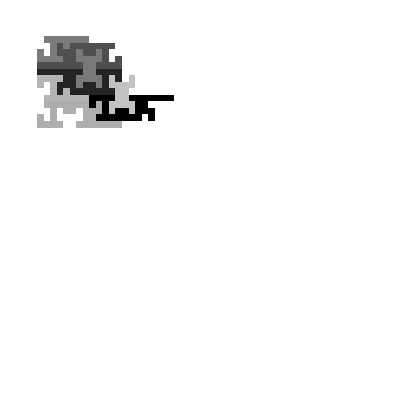

```mathematica
growSideStep[universe,tiles,1,visualUniverse]
```

```mathematica
overlay[universe,{{usedrange[[1,2]]-ibound,usedrange[[1,2]]-ibound+20},{1,1+20}}]
```

-Graphics-

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

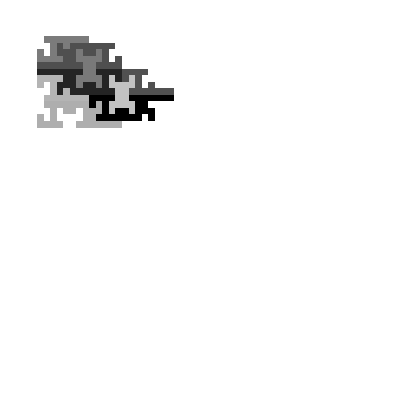

```mathematica
growSideStep[universe,tiles,1,visualUniverse]
```

```mathematica
overlay[universe,{{usedrange[[1,2]]-ibound,usedrange[[1,2]]-ibound+20},{1,1+20}}]
```

-Graphics-

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

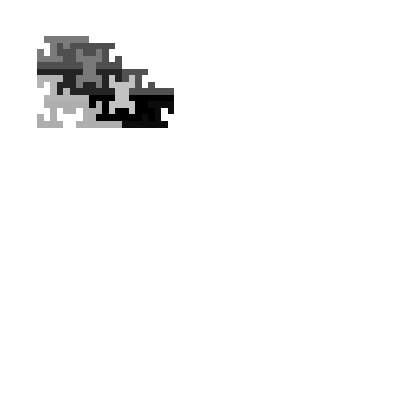

```mathematica
growSideStep[universe,tiles,1,visualUniverse]
```

```mathematica
overlay[universe,{{usedrange[[1,2]]-ibound,usedrange[[1,2]]-ibound+20},{1,1+20}}]
```

-Graphics-

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

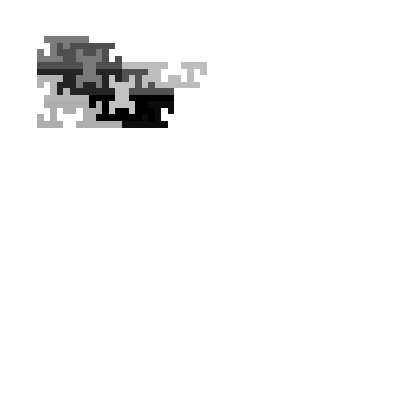

```mathematica
growSideStep[universe,tiles,1,visualUniverse]
```

```mathematica
overlay[universe,{{usedrange[[1,2]]-ibound,usedrange[[1,2]]-ibound+20},{1,1+20}}]
```

-Graphics-

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

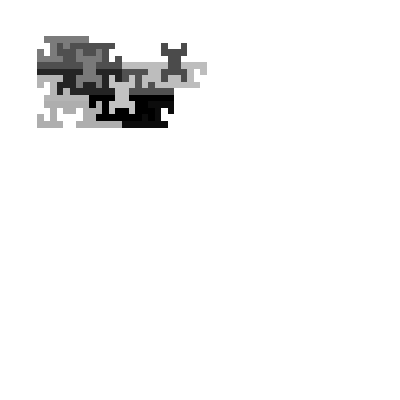

```mathematica
growSideStep[universe,tiles,1,visualUniverse]
```

```mathematica
overlay[universe,{{usedrange[[1,2]]-ibound,usedrange[[1,2]]-ibound+20},{1,1+20}}]
```

-Graphics-

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

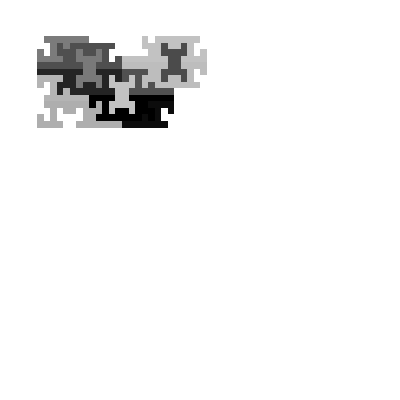

```mathematica
growSideStep[universe,tiles,1,visualUniverse]
```

```mathematica
overlay[universe,{{1,1+20},{usedrange[[2,2]]-ibound,usedrange[[2,2]]-ibound+20}}]
```

-Graphics-

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

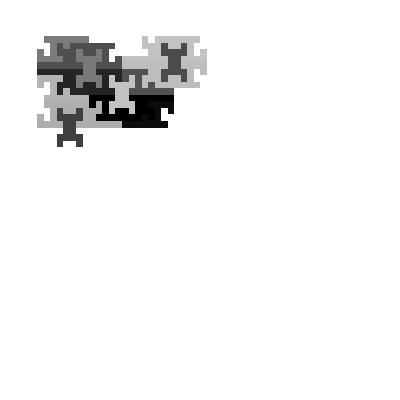

```mathematica
growDownStep[universe,tiles,1,visualUniverse]
```

```mathematica
overlay[universe,{{1,1+20},{usedrange[[2,2]]-ibound,usedrange[[2,2]]-ibound+20}}]
```

-Graphics-

```mathematica
overlay[universe,{{1,1+20},{usedrange[[2,2]]-ibound,usedrange[[2,2]]-ibound+20}}]
```

-Graphics-

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

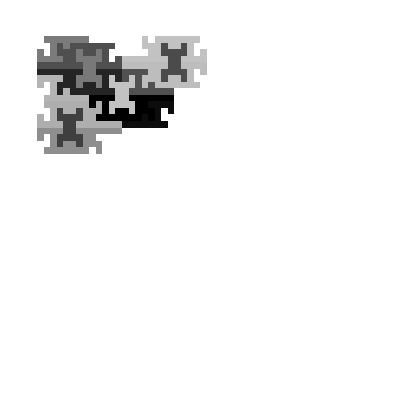

```mathematica
growDownStep[universe,tiles,1,visualUniverse]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

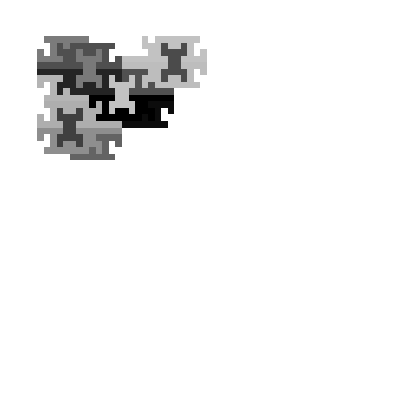

```mathematica
growDownStep[universe,tiles,1,visualUniverse]
```

```mathematica
space//ArrayPlot
```

-Graphics-

```mathematica
addNextTile[space,tiles]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

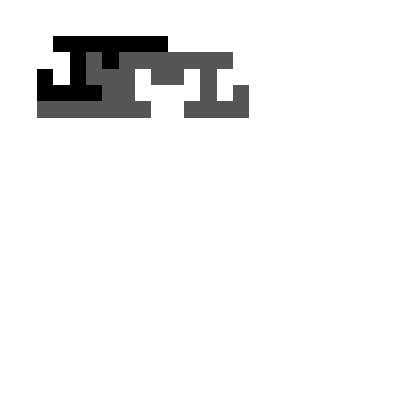

```mathematica
addNextTileLocal[]
```

```mathematica
scores//MatrixForm
```

(∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1.49333
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1.49333
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1.49333
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1.23529 | ∞ | 1.49333
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1.49333
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1.6
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1.60627 | 1.70667
∞ | ∞ | ∞ | 1.3 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1.70667 | 1.81333
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1.92
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2.02667
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1.88235 | 2.00784 | 2.13333)

```mathematica
tile=tiles[[9]];
regiontoscan=scanRange[tile,space];
scores=Transpose[Table[score[addTile[tile,space,{x,y}]],{x,regiontoscan[[1,1]],regiontoscan[[1,2]]},{y,regiontoscan[[2,1]],regiontoscan[[2,2]]}]];
scoresImg=Transpose[Table[scoreImg[addTile[tile,space,{x,y}]],{x,regiontoscan[[1,1]],regiontoscan[[1,2]]},{y,regiontoscan[[2,1]],regiontoscan[[2,2]]}]];
scores=scores/Max[Cases[{Infinity,1,2,4,10},_Integer]]*(1-scoresImg);
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

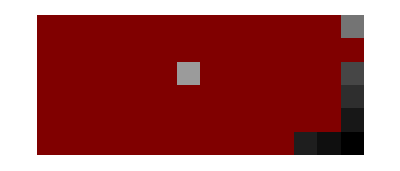

```mathematica
scores//ArrayPlot
```

```mathematica
usedSpace[universe]//ArrayPlot
```

-Graphics-

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

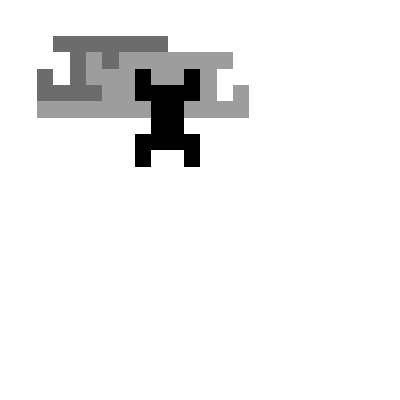

```mathematica
addNextTileLocal[]
```

```mathematica
space//ArrayPlot
```

-Graphics-

```mathematica
innerBound[space]
```

4

```mathematica
usedSpace[space]//ArrayPlot
```

-Graphics-

```mathematica
Dimensions[usedSpace[space]]
```

{8,13}

```mathematica
overlay[usedSpace[space],{{4,5},{4,7}}]
```

Thread::tdlen: Objects of unequal length in {{0,1,1,1,1,1,1,1,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,1,0},{1,0,1,1,1,1,1,1,1,1,1,0,0},{1,1,1,1,1,1,1,1,1,1,1,0,1},{1,1,1,1,1,1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,1,1,0,0,0,0},{0,0,0,0,0,0,1,1,1,1,0,0,0},{0,0,0,0,0,0,1,0,0,1,0,0,0}}+{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,2,2,0,0,0},{0,0,0,2,2,0,0,0},«3»,{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}} cannot be combined.

ArrayPlot::mat: Argument {{0,1,1,1,1,1,1,1,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,1,0},{1,0,1,1,1,1,1,1,1,1,1,0,0},{1,1,1,1,1,1,1,1,1,1,1,0,1},{1,1,1,1,1,1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,1,1,0,0,0,0},{0,0,0,0,0,0,1,1,1,1,0,0,0},{0,0,0,0,0,0,1,0,0,1,0,0,0}}+{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,2,2,0,0,0},{0,0,0,2,2,0,0,0},«3»,{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}} at position 1 is not a list of lists.

ArrayPlot[{{0,1,1,1,1,1,1,1,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,1,0},{1,0,1,1,1,1,1,1,1,1,1,0,0},{1,1,1,1,1,1,1,1,1,1,1,0,1},{1,1,1,1,1,1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,1,1,0,0,0,0},{0,0,0,0,0,0,1,1,1,1,0,0,0},{0,0,0,0,0,0,1,0,0,1,0,0,0}}+{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,2,2,0,0,0},{0,0,0,2,2,0,0,0},{0,0,0,2,2,0,0,0},{0,0,0,2,2,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}]

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

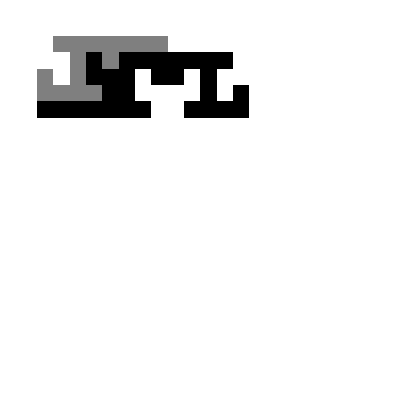

```mathematica
addNextTileLocal[]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

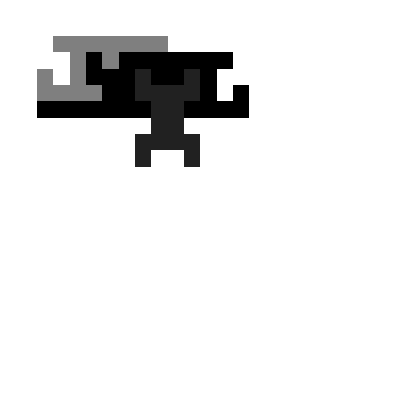

```mathematica
addNextTileLocal[]
```

```mathematica
space//ArrayPlot
```

-Graphics-

```mathematica
universe//ArrayPlot
```

-Graphics-

```mathematica
overlay[universe,{{1,20},{1,20}}]
```

-Graphics-

```mathematica
tile=tiles[[13]];
regiontoscan=scanRange[tile,space];
scores=Transpose[Table[score[addTile[tile,space,{x,y}]],{x,regiontoscan[[1,1]],regiontoscan[[1,2]]},{y,regiontoscan[[2,1]],regiontoscan[[2,2]]}]];
scoresImg=Transpose[Table[scoreImg[addTile[tile,space,{x,y}]],{x,regiontoscan[[1,1]],regiontoscan[[1,2]]},{y,regiontoscan[[2,1]],regiontoscan[[2,2]]}]];
scores=scores/Max[Cases[{Infinity,1,2,4,10},_Integer]]*(1-scoresImg);
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

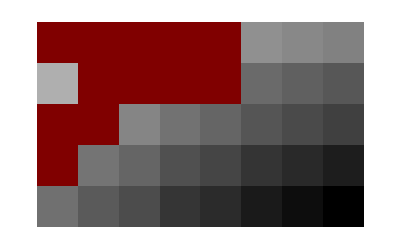

```mathematica
scores//ArrayPlot
```

```mathematica
usedSpace[space]//ArrayPlot
```

-Graphics-

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

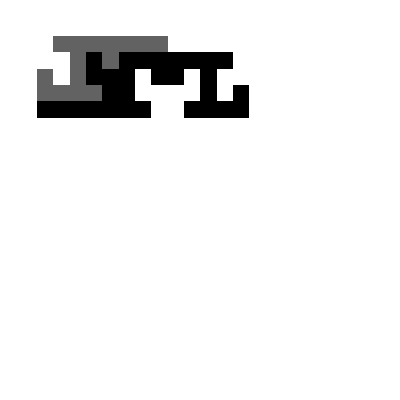

```mathematica
addNextTileLocal[]
```

```mathematica
putUniverse[universe,space,{1,1}]
```

-Graphics-

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

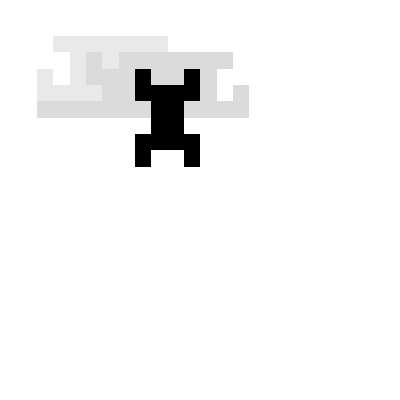

```mathematica
addNextTileLocal[]
```

```mathematica
scores//ArrayPlot
```

-Graphics-

```mathematica
tile=tiles[[9]];
regiontoscan=scanRange[tile,space];
scores=Transpose[Table[score[addTile[tile,space,{x,y}]],{x,regiontoscan[[1,1]],regiontoscan[[1,2]]},{y,regiontoscan[[2,1]],regiontoscan[[2,2]]}]];
scoresImg=Transpose[Table[scoreImg[addTile[tile,space,{x,y}]],{x,regiontoscan[[1,1]],regiontoscan[[1,2]]},{y,regiontoscan[[2,1]],regiontoscan[[2,2]]}]];
scores=scores/Max[Cases[{Infinity,1,2,4,10},_Integer]]*(1-scoresImg);
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

```mathematica
scores//ArrayPlot
```

-Graphics-

```mathematica
universe//ArrayPlot
```

-Graphics-

```mathematica
space=takeUniverse[universe,{1,1},{19,19}]
```

{{0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,0,1,1,1,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,0,0,0,0,1,0,1,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,0,0,1,1,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
space//ArrayPlot
```

-Graphics-

```mathematica
overlay[universe,{{1,19},{1,19}}]
```

-Graphics-

```mathematica
usedSpace[universe]//ArrayPlot
```

-Graphics-

```mathematica
putUniverse[universe,space,{1,1}]
```

-Graphics-

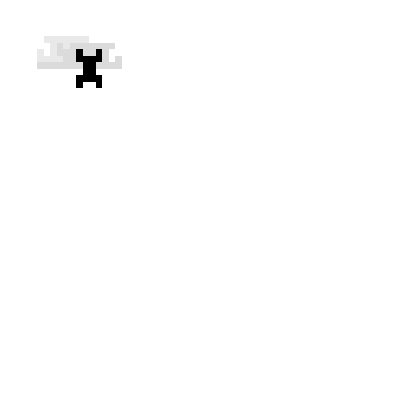

```mathematica
putUniverse[visualUniverse,visualSpace,{1,1}]
```

```mathematica
overlay[universe,{{1,19},{1,19}}]
```

-Graphics-

```mathematica
usedSpace[universe]//ArrayPlot
```

-Graphics-

```mathematica
tile=tiles[[15]];
regiontoscan=scanRange[tile,space];
scores=Transpose[Table[score[addTile[tile,space,{x,y}]],{x,regiontoscan[[1,1]],regiontoscan[[1,2]]},{y,regiontoscan[[2,1]],regiontoscan[[2,2]]}]];
scoresImg=Transpose[Table[scoreImg[addTile[tile,space,{x,y}]],{x,regiontoscan[[1,1]],regiontoscan[[1,2]]},{y,regiontoscan[[2,1]],regiontoscan[[2,2]]}]];
scores=scores/Max[Cases[{Infinity,1,2,4,10},_Integer]]*(1-scoresImg);
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

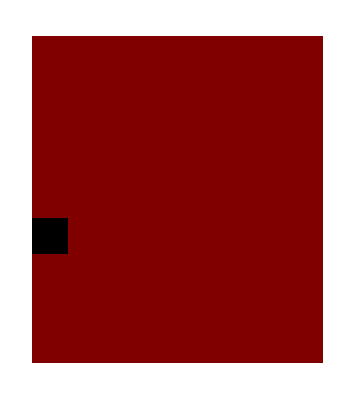

```mathematica
scores//ArrayPlot
```

```mathematica
space//ArrayPlot
```

-Graphics-

```mathematica
putUniverse[universe,space,]
```

```mathematica
Dilation[EdgeDetect[-Graphics-],1]
```

-Graphics-

```mathematica
putUniverse[universe,space,{1,1}]
```

-Graphics-

```mathematica
overlay[universe,{{1,19},{1,19}}]
```

-Graphics-

```mathematica
space//usedSpace//ArrayPlot
```

-Graphics-

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

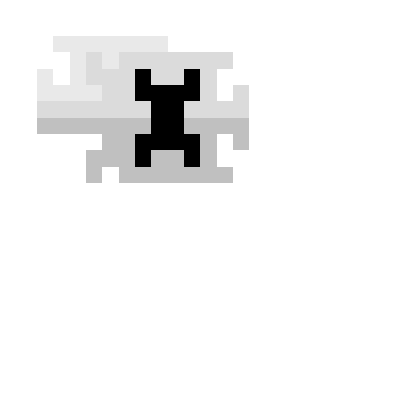

```mathematica
addNextTileLocal[]
```

```mathematica
putUniverse[universe,space,{1,1}]
```

-Graphics-

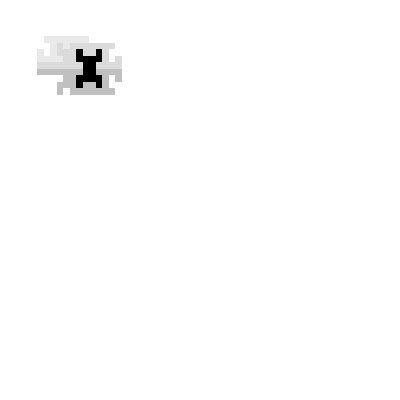

```mathematica
putUniverse[visualUniverse,visualSpace,{1,1}]
```

```mathematica
universe//ArrayPlot
```

-Graphics-

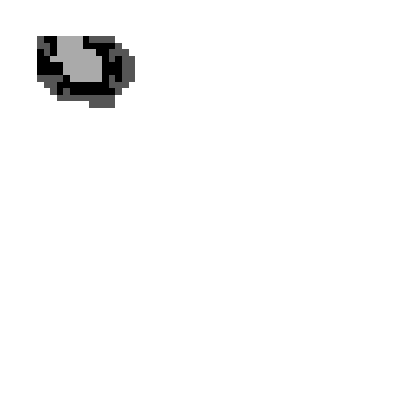

```mathematica
ArrayPlot[ImageData[Dilation[EdgeDetect[Image[universe,"Bit"]],1]]+0.5*universe]
```

```mathematica
boundary=Position[ImageData[Dilation[EdgeDetect[Image[universe,"Bit"]],1]],1]
```

{{1,1},{1,2},{1,3},{1,8},{1,9},{1,10},{1,11},{1,12},{2,1},{2,2},{2,3},{2,8},{2,9},{2,10},{2,11},{2,12},{2,13},{3,1},{3,2},{3,3},{3,10},{3,11},{3,12},{3,13},{3,14},{4,1},{4,2},{4,11},{4,12},{4,13},{4,14},{4,15},{5,1},{5,2},{5,3},{5,4},{5,11},{5,12},{5,13},{5,14},{5,15},{6,1},{6,2},{6,3},{6,4},{6,11},{6,12},{6,13},{6,14},{6,15},{7,1},{7,2},{7,3},{7,4},{7,5},{7,11},{7,12},{7,13},{7,14},{7,15},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,8},{8,9},{8,10},{8,11},{8,12},{8,13},{8,14},{9,3},{9,4},{9,5},{9,6},{9,7},{9,8},{9,9},{9,10},{9,11},{9,12},{9,13},{10,4},{10,5},{10,6},{10,7},{10,8},{10,9},{10,10},{10,11},{10,12},{11,9},{11,10},{11,11},{11,12}}

```mathematica
dimension=Ceiling[1.5*(First/@Dimensions/@tiles//Max)];
```

```mathematica
SetSharedVariable[minMinScores,minScores];
minMinScores={};
minScores={};
ParallelMap[
space=takeUniverse[universe,{#[[1]],#[[2]]},{dimension,dimension}];
Map[
tile=#;
regiontoscan=scanRange[tile,space];
scores=Transpose[Table[score[addTile[tile,space,{x,y}]],{x,regiontoscan[[1,1]],regiontoscan[[1,2]]},{y,regiontoscan[[2,1]],regiontoscan[[2,2]]}]];
scoresImg=Transpose[Table[scoreImg[addTile[tile,space,{x,y}]],{x,regiontoscan[[1,1]],regiontoscan[[1,2]]},{y,regiontoscan[[2,1]],regiontoscan[[2,2]]}]];
scores=scores/Max[Cases[{Infinity,1,2,4,10},_Integer]]*(1-scoresImg);
newPos=Reverse[First[Take[Position[scores,Min[scores]],1]]]+First/@regiontoscan-{1,1};
AppendTo[minScores,{Min[scores],addTile[tile,space,newPos]}];
&,tiles];
AppendTo[minMinScores,First[SortBy[minScores,#[[1]]&]]];
&,boundary
]
```

Table::iterb: Iterator {x,∞,-∞} does not have appropriate bounds.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

Table::iterb: Iterator {x,∞,-∞} does not have appropriate bounds.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

Thread::tdlen: Objects of unequal length in {}+{∞,∞}+{-1,-1} cannot be combined.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

Table::iterb: Iterator {x,∞,-∞} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {}+{-1,-1}+{∞,∞} cannot be combined.

Thread::tdlen: Objects of unequal length in {}+{∞,∞}+{-1,-1} cannot be combined.

Thread::tdlen: Objects of unequal length in {}+{-1,-1}+{∞,∞} cannot be combined.

Thread::tdlen: Objects of unequal length in {}+{∞,∞}+{-1,-1} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {}+{-1,-1}+{∞,∞} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

Table::iterb: Iterator {x,∞,-∞} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {}+{-1,-1}+{∞,∞} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

$Aborted

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

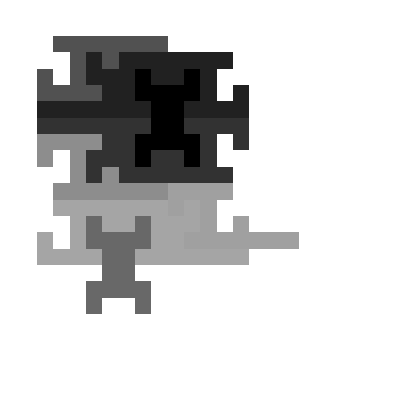

```mathematica
addNextTileLocal[]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

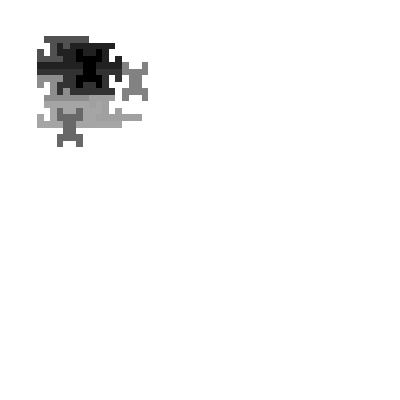

```mathematica
growSideStep[universe,tiles,1,visualUniverse]
```

```mathematica
universe=universeBackup;visualUniverse=visualUniverseBackup;
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

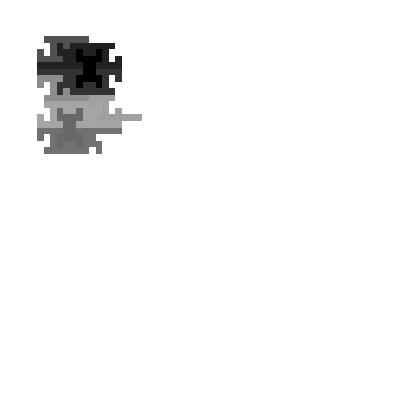

```mathematica
growDownStep[universe,tiles,1,visualUniverse]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

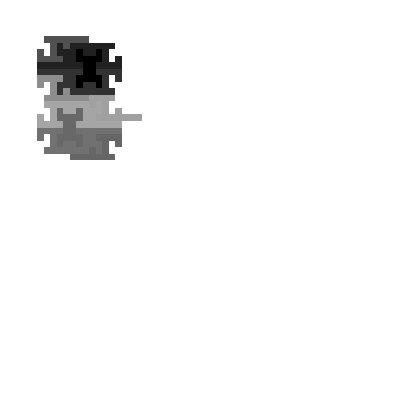

```mathematica
growDownStep[universe,tiles,1,visualUniverse]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

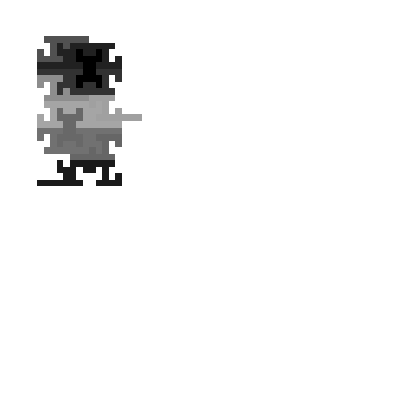

```mathematica
growDownStep[universe,tiles,1,visualUniverse]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

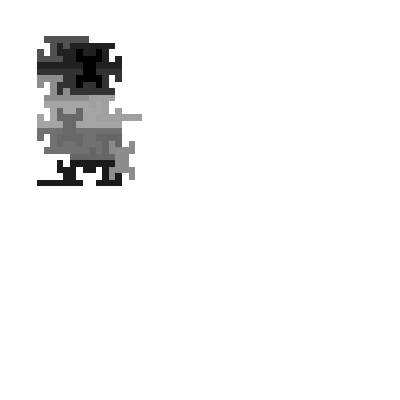

```mathematica
growDownStep[universe,tiles,1,visualUniverse]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

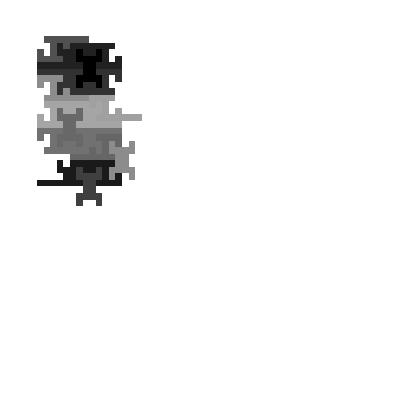

```mathematica
growDownStep[universe,tiles,1,visualUniverse]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

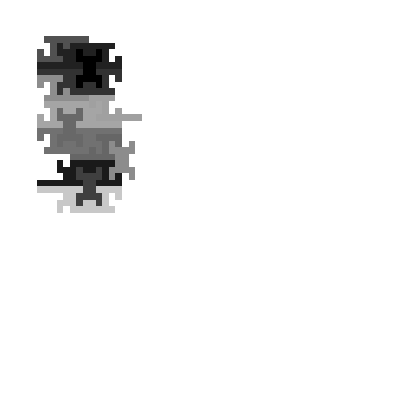

```mathematica
growDownStep[universe,tiles,1,visualUniverse]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

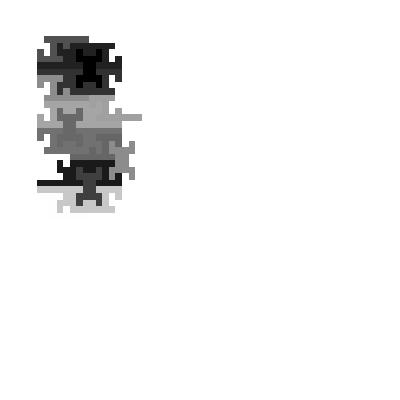

```mathematica
growDownStep[universe,tiles,1,visualUniverse]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

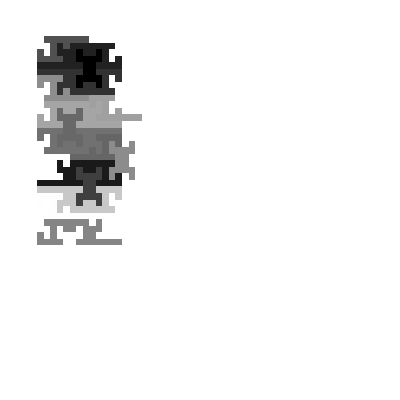

```mathematica
growDownStep[universe,tiles,1,visualUniverse]
```

```mathematica
growDownStep[universe,tiles,1,visualUniverse]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

$Aborted

```mathematica
growDownStep[universe,tiles,1,visualUniverse]
```

```mathematica
innerBound[universe]
```

7

```mathematica
usedRange[universe]
```

{{1,16},{1,32}}

```mathematica
overlay[universe,{{1,19},{25,44}}]
```

-Graphics-

```mathematica
spaced//ArrayPlot
```

-Graphics-

```mathematica
addNextTile[spaced,tiles]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

{{1,1,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
ArrayPlot[%]
```

-Graphics-

```mathematica
space//ArrayPlot
```

-Graphics-

```mathematica
newspaced={{1,1,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}};
```

```mathematica
RandomReal[]*(newspaced-spaced),{}
```

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.0718401,0.,0.,0.0718401,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.0718401,0.0718401,0.0718401,0.0718401,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.0718401,0.0718401,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.0718401,0.0718401,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.0718401,0.0718401,0.0718401,0.0718401,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.0718401,0.,0.,0.0718401,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

```mathematica
visualSpace//ArrayPlot
```

-Graphics-

```mathematica
space//ArrayPlot
```

-Graphics-

```mathematica
space=takeUniverse[universe,{1,25},{20,20}]
```

{{1,1,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,1,1,0,1,1,1,0,0,0,0,0,0,0,0,0,0},{1,0,1,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,1,1,1,1,1,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
Dimensions[space]
```

{20,20}

```mathematica
space//ArrayPlot
```

-Graphics-

```mathematica
visualSpace=takeUniverse[visualUniverse,{1,25},{20,20}];
```

```mathematica
addNextTile[space,tiles]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

{{1,1,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
newspace={{1,1,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}};
```

```mathematica
visualSpace=visualSpace+RandomReal[]*(newspace-space)
```

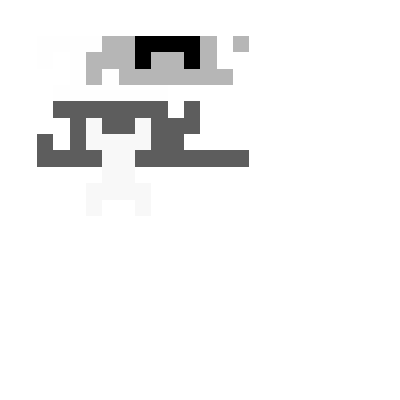

```mathematica
ArrayPlot[visualSpace]
```

```mathematica
visualUniverse//ArrayPlot
```

-Graphics-

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

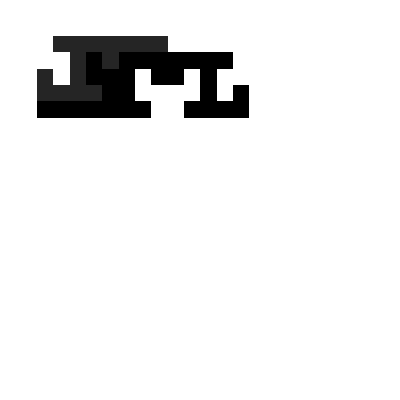

```mathematica
addNextTileLocal[]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

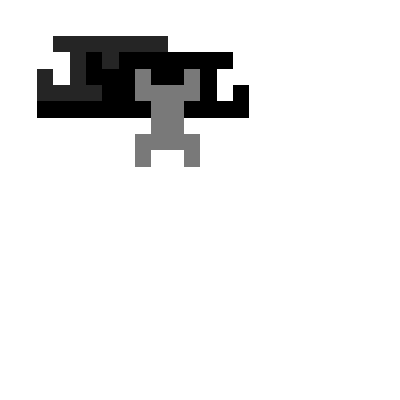

```mathematica
addNextTileLocal[]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

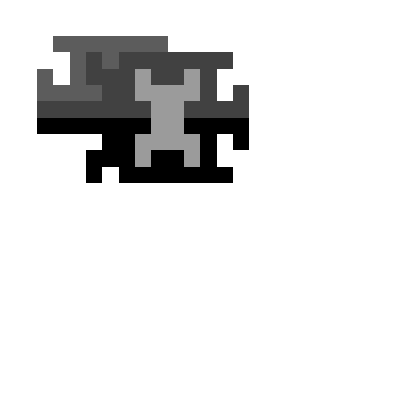

```mathematica
addNextTileLocal[]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

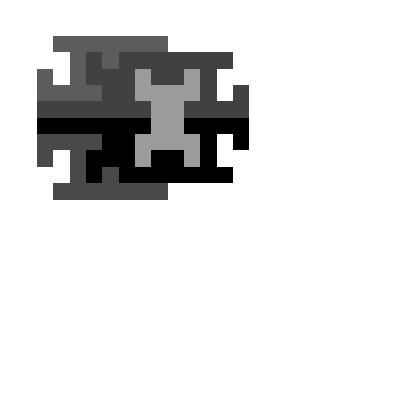

```mathematica
addNextTileLocal[]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

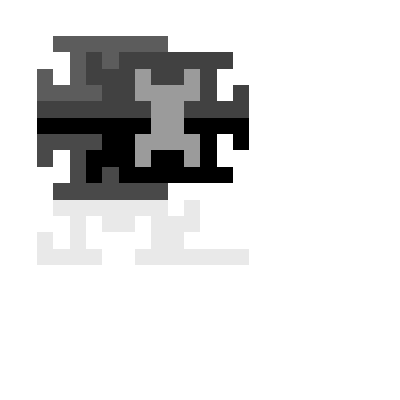

```mathematica
addNextTileLocal[]
```

```mathematica
putUniverse[universe,space,{1,1}]
```

-Graphics-

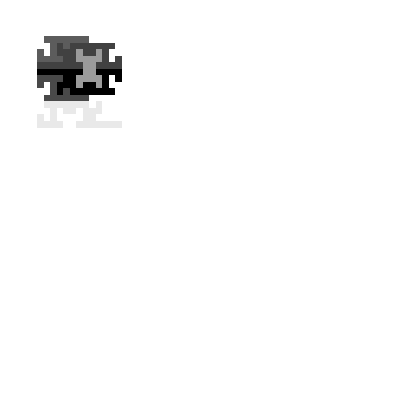

```mathematica
putUniverse[visualUniverse,visualSpace,{1,1}]
```

```mathematica
showUniverse[universe,tiles,{1,9},visualUniverse]//ArrayPlot
```

-Graphics-

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

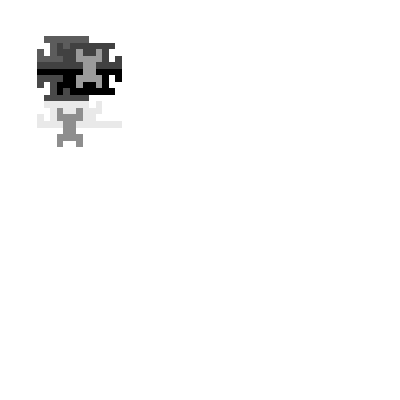

```mathematica
growUniverse[universe,tiles,{1,9},visualUniverse]
```

```mathematica
showUniverse[universe,tiles,{1,9},visualUniverse]//ArrayPlot
```

-Graphics-

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

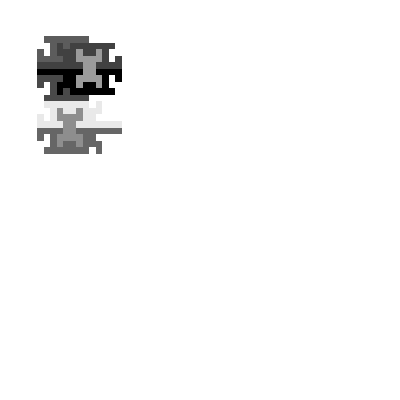

```mathematica
growUniverse[universe,tiles,{1,9},visualUniverse]
```

```mathematica
growUniverse[universe,tiles,{1,9},visualUniverse]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

-Graphics-

```mathematica
growUniverse[universe,tiles,{1,9},visualUniverse]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

-Graphics-

```mathematica
growUniverse[universe,tiles,{1,11},visualUniverse]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

-Graphics-

```mathematica
growUniverse[universe,tiles,{1,15},visualUniverse]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

-Graphics-

```mathematica
growUniverse[universe,tiles,{10,1},visualUniverse]
```

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

ArrayPlot::mat: Argument 0 at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

-Graphics-

```mathematica
overlay[universe,{{10,14},{15,19}}]
```

-Graphics-

```mathematica
visualUniverse[[15,17]]=0
```

0

```mathematica
universe=universeBackup;visualUniverse=visualUniverseBackup;
```

```mathematica
visualUniverse//ArrayPlot
```

-Graphics-

```mathematica
universe//ArrayPlot
```

-Graphics-

```mathematica
overlay[universe,{{10,10},{17,17}}]
```

-Graphics-